```mathematica
heart=Import["/Users/admin/Documents/Intro to Data Science/Project data/heart 2.csv"](*fedesoriano.(September 2021).Heart Failure Prediction Dataset.Retrieved[Date Retrieved] from https://www.kaggle.com/fedesoriano/heart-failure-predictionhttps://www.kaggle.com/fedesoriano/heart-failure-predictionNonehttps://www.kaggle.com/fedesoriano/heart-failure-predictionHyperlinkActionRecycledHyperlinkActive. A csv file will be emailed to you*)
```

{{Age,Sex,ChestPainType,RestingBP,Cholesterol,FastingBS,RestingECG,MaxHR,ExerciseAngina,Oldpeak,ST_Slope,HeartDisease},{40,M,ATA,140,289,0,Normal,172,N,0,Up,0},{49,F,NAP,160,180,0,Normal,156,N,1,Flat,1},{37,M,ATA,130,283,0,ST,98,N,0,Up,0},911,{68,M,ASY,144,193,1,Normal,141,N,3.4,Flat,1},{57,M,ASY,130,131,0,Normal,115,Y,1.2,Flat,1},{57,F,ATA,130,236,0,LVH,174,N,0,Flat,1},{38,M,NAP,138,175,0,Normal,173,N,0,Up,0}}
 |  |  |  |

## Variables

Age:  age of the subjects (years)

Sex:  Sex of the patients (M:Male, F:Female)

ChestPainType: The type of Angina (chest pain) reported by subjects (TA:Typical Angina,  ATA:Atypical Angina,  NAP:Non-Anginal Pain, ASY:Asymptomatic).

RestingBP: Resting blood pressure (mm/Hg)

Cholesterol: Serum cholesterol (mg/dl)

FastingBS: Fasting serum blood sugar (mg/dl)

RestingECG:This column describes the resting ECG data, ECG measure the electrical activity of the heart and the ECG output normal shows a wave heart issues are usually diagnosed by seeing if the wave looks normal or not;  Normal : Normal,  ST : having ST -T wave abnormality (T wave inversions and/or ST elevation or depression of > 0.05 mV)  These abnormalities can indicate a cardiac pathology but can be normal as well ,
 LVH : showing probable or definite left ventricular hypertrophy by Estes’ criteria, Don’t worry about what Estes criteria is, but left ventricular hypertrophy means that the walls of the left ventricle of the heart is enlarged, this is not good because it can lead to heart failure.

MaxHR: Maximum heart rate achieved during exercise stress testing (bpm).

ExerciseAngina: Presence of chest pain during exercise (N: no exercise angina, Y: exercise angina present)

Oldpeak: represents the  magnitude of a st depression on ECG (mm).

-Graphics-

(Picture from: Chowdhury et al, 2019 )

ST_Slope: This describes the slope of the peak exercise ST segment. (Up: upsloping, Flat:flat, Down:downsloping) see below.

-Graphics--Graphics-

The ST segment is in orange if it rises sharply, ie. if the value is Up ,that is normal during exercise, flat and downsloping is abnormal and could be a indicator of cardiac issues , you can read more at LINKhttps://www.ncbi.nlm.nih.gov/pmc/articles/PMC1123032/#:~:text=The%20J%20point%20(the%20point,exercise%20therefore%20slopes%20sharply%20upwards.Nonehttps://www.ncbi.nlm.nih.gov/pmc/articles/PMC1123032/#:~:text=The%20J%20point%20(the%20point,exercise%20therefore%20slopes%20sharply%20upwards.HyperlinkActionRecycledHyperlinkActive.

HeartDisease: Is the subject diagnosed with heart disease or not (0: No Heart Disease, negative diagnosis 1: positive diagnosis )

## Duplicates and missing values

```mathematica
DuplicateFreeQ[heart] (*The data is free of duplicates*)
```

True

```mathematica
Cases[heart, {___,"" ,___ }] (*There are no missing values in the dataset*)
```

{}

```mathematica
Cases[heart, {___,_Missing,___}](*There are no missing values*)
```

{}

```mathematica
Exploratory data analysis
```

The First task is to carry out data exploration exercises  in order to determine the structure of data, and relationships between variables.How does each independent variable  influence the outcome of the dependant variable, the dependant variable being the presence or absence of heart disease.

```mathematica
heart2 =AssociationThread[heart[[1]]-> #]& /@ heart[[2;;]](*Making an association dataset for easy querying and function building*)
```

{<|Age→40,Sex→M,ChestPainType→ATA,RestingBP→140,Cholesterol→289,FastingBS→0,RestingECG→Normal,MaxHR→172,ExerciseAngina→N,Oldpeak→0,ST_Slope→Up,HeartDisease→0|>,<|Age→49,Sex→F,ChestPainType→NAP,RestingBP→160,Cholesterol→180,FastingBS→0,RestingECG→Normal,MaxHR→156,ExerciseAngina→N,Oldpeak→1,ST_Slope→Flat,HeartDisease→1|>,915,<|Age→38,Sex→M,ChestPainType→NAP,RestingBP→138,Cholesterol→175,FastingBS→0,RestingECG→Normal,MaxHR→173,ExerciseAngina→N,Oldpeak→0,ST_Slope→Up,HeartDisease→0|>}
 |  |  |  |

```mathematica
variablelist =Keys[heart2]// DeleteDuplicates// Flatten (*What are the variables we have?*)
```

{Age,Sex,ChestPainType,RestingBP,Cholesterol,FastingBS,RestingECG,MaxHR,ExerciseAngina,Oldpeak,ST_Slope,HeartDisease}

```mathematica
univariate[variable_,name_]:= Module[{list},(*first argument is a String with the column name needed, second argument is the desired name for the new list*)
list = Query[ All,variable] [heart2];  (*the first argument string will be inputed here and this column will be isolated from the heart2 dataset*)
 name= list; 
Return[name]] (*Assign extracted list to the second argument*)
```

```mathematica
datalist = {loneage,lonesex,lonepain,lonebp,lonechol,lonebs,loneecg,lonehr,loneangina,loneold,lonest,lonehd };(*list names to assign extracted data to*)
```

```mathematica
MapThread[univariate,{variablelist, datalist}];(*Thread the univariate function onto variable list as first argument and datalist as second argument*)
```

```mathematica
continousdatalist = {loneage,lonebp,lonechol,lonehr,loneold};(*List of lists containing continous features*)
```

```mathematica
summarydata={Map[Length, continousdatalist],(*Map Length onto continousdatalist*)
N[Map[Mean, continousdatalist]],(*Map Length onto continousdatalist*)
N[Map[StandardDeviation, continousdatalist]],
N[Map[Min, continousdatalist]],
N[Map[Quantile[#,1/4]&, continousdatalist]],
N[Map[Quantile[#,1/2]&, continousdatalist]],
N[Map[Quantile[#,3/4]&, continousdatalist]],
N[Map[Max, continousdatalist]]}
```

{{918,918,918,918,918},{53.5109,132.397,198.8,136.809,0.887364},{9.43262,18.5142,109.384,25.4603,1.06657},{28.,0.,0.,60.,-2.6},{47.,120.,173.,120.,0.},{54.,130.,223.,138.,0.6},{60.,140.,267.,156.,1.5},{77.,200.,603.,202.,6.2}}

```mathematica
rowheadings= {"Count","Mean","Standard Deviation", "Min", "25% Quantile", "50% Quantile", "75% Quantile", "Max"}
```

{Count,Mean,Standard Deviation,Min,25% Quantile,50% Quantile,75% Quantile,Max}

```mathematica
columnheadings = {"Age","RestingBP","Cholesterol","MaxHR","Oldpeak"}
```

{Age,RestingBP,Cholesterol,MaxHR,Oldpeak}

```mathematica
TableForm[summarydata, TableHeadings->{rowheadings,columnheadings}](*Summary statistics of the continous variables*)
```

| Age | RestingBP | Cholesterol | MaxHR | Oldpeak
Count | 918 | 918 | 918 | 918 | 918
Mean | 53.5109 | 132.397 | 198.8 | 136.809 | 0.887364
Standard Deviation | 9.43262 | 18.5142 | 109.384 | 25.4603 | 1.06657
Min | 28. | 0. | 0. | 60. | -2.6
25% Quantile | 47. | 120. | 173. | 120. | 0.
50% Quantile | 54. | 130. | 223. | 138. | 0.6
75% Quantile | 60. | 140. | 267. | 156. | 1.5
Max | 77. | 200. | 603. | 202. | 6.2

### Univariate Analysis

```mathematica
Age
```

```mathematica
loneage// Short
```

{40,49,37,48,54,39,45,54,37,48,37,58,39,49,42,54,38,43,60,36,43,44,49,44,40,36,53,«864»,66,39,57,58,57,47,55,35,61,58,58,58,56,56,67,55,44,63,63,41,59,57,45,68,57,57,38}

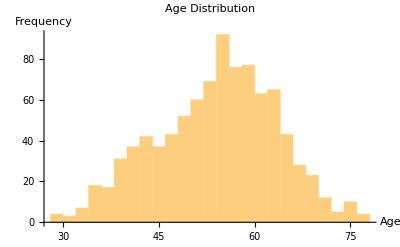

```mathematica
Histogram[loneage, AxesLabel->{"Age", "Frequency"}, PlotLabel->"Age Distribution", LabelStyle->Directive[Bold, Thick]]
```

Age seems to be normally distributed, however there is a slight right skew, A distribution fit test will be carried out to determine if the data is Normally distributed. The goodness of fit test will be carried out with the null hypothesis that the data is distributed according to Gaussian distribution

```mathematica
agenormtest =DistributionFitTest[loneage,Automatic, "HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
agenormtest["TestDataTable"]
```

| Statistic | P-Value
Cramér-von Mises | 0.495594 | 2.20243×10^-6

The null hypothesis that the data is distributed according to the NormalDistribution[x, y] is rejected at the 5 percent level based on the Cramér-von Mises test. The data is not normally distributed.

```mathematica
Gender
```

```mathematica
lonesex // Short
```

{M,F,M,F,M,M,F,M,M,F,F,M,M,M,F,F,M,F,M,M,«879»,M,M,F,M,M,M,M,F,M,M,F,M,M,F,M,M,M,F,M}

```mathematica
tally[column_List]:= AssociationThread[Tally[column][[All,1]]-> Tally[column][[All,2]]](*Function for automatically tallying features containing categorical data, the aurgument to be entered is the list containing feature values *)
```

```mathematica
gengdata=tally[lonesex](*tally the values of lonesex, M: Male, F:Female*)
```

<|M→725,F→193|>

```mathematica
GraphicsRow[{BarChart[gengdata,{ChartStyle-> "Pastel", ChartLabels->Automatic, AxesLabel-> "Counts", PlotLabel->"Gender Distribution", LabelStyle->Directive[Bold, Thick]}],PieChart[{gengdata},ChartStyle->"Pastel", ChartLabels->Automatic]}]
```

-Graphics-

```mathematica
{{"Male", PercentForm[725/(725+193)//N]},{"Female", PercentForm[193/(725+193)//N]}}// TableForm
```

Male | 78.98%
Female | 21.02%

Males are overrepresented in the data with approximately 79% of patients being male, with bi-variate analysis we can check how gender is distributed among diagnostic groups.

#### Chest Pain Type

```mathematica
paindata=tally[lonepain]
```

<|ATA→173,NAP→203,ASY→496,TA→46|>

```mathematica
GraphicsRow[{BarChart[paindata,{ChartStyle-> "Pastel", ChartLabels->Automatic, AxesLabel-> "Counts", PlotLabel->"Distribution of chest pain type", LabelStyle->Directive[Bold, Thick]}],PieChart[{paindata},ChartStyle-> "Pastel", ChartLabels->Automatic] }]
```

-Graphics-

Most of the patients (>50%)  report having no symptoms of heart pain.

Atypical Angina is the most common anginal pain .

```mathematica
RestingBP
```

```mathematica
lonebp//Short
```

{140,160,130,138,150,120,130,110,140,120,130,136,120,140,115,120,110,120,100,120,«878»,122,148,114,170,125,130,120,152,132,120,140,124,120,164,140,110,144,130,130,138}

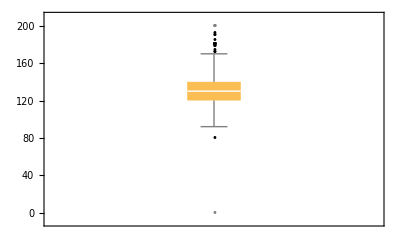

```mathematica
BoxWhiskerChart[lonebp, "Outliers",ChartLabels->{ " ","Resting Blood Pressure (mmHg)"}, ChartLabels->"Resting Blood Pressure Distribution"]
```

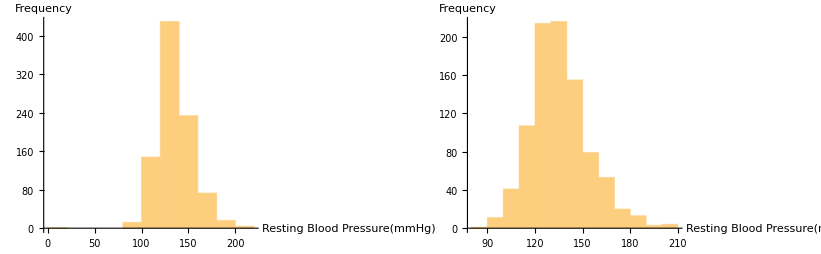

```mathematica
GraphicsRow[{Histogram[lonebp, AxesLabel-> {"Resting Blood Pressure(mmHg)", "Frequency"}, ImageSize->Large],Histogram[Drop[Sort[lonebp],1],15,AxesLabel-> {"Resting Blood Pressure(mmHg)", "Frequency"}, ImageSize->Large]}](*There is a blood pressure reading of 0 in the data that is skewing the distribution, this is likely to be an outlier, both due to statistical implications and biological, since a person with a blood pressure of 0 will be dead*)
```

If the 0 outlier is removed the data follows a slight leftwards skew , the values above 180 could be considered outliers, however they are biologically feasible. This data is not normally distributed.

```mathematica
Cholesterol
```

```mathematica
lonechol//Short
```

{289,180,283,214,195,339,237,208,207,284,211,164,204,234,211,273,196,201,248,267,«878»,192,203,318,225,220,221,240,212,342,169,187,197,157,176,241,264,193,131,236,175}

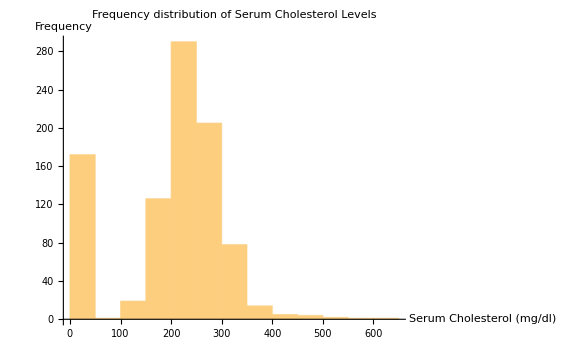

```mathematica
Histogram[lonechol,AxesLabel->{"Serum Cholesterol (mg/dl)","Frequency"}, ImageSize->Large, PlotLabel->"Frequency distribution of Serum Cholesterol Levels"] (*There a lot of 0 values, though the highest frequency seems to be within the 200- 250 interval, most of the values are at 0*)
```

```mathematica
choltally =Tally[lonechol]// Sort ;
```

```mathematica
Dataset[choltally]// Short (*There are 172 , 0 values*)
```

```mathematica
choltallyassociation =AssociationThread[choltally[[All,1]] -> choltally[[All,2]]];
```

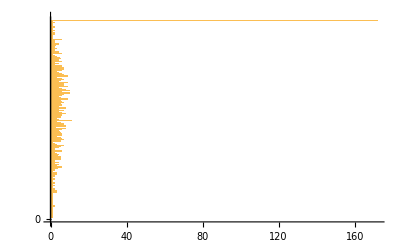

```mathematica
BarChart[Reverse[choltallyassociation],BarSpacing-> 1, BarOrigin->Left, ImageSize->Full,Ticks-> {Automatic, {0,600}}](*There is a disproportionatly high number of 0 values in the data*)
```

Just for the purpose of visualising the data, I will try and drop the 0 values. This will help see the true distribution of the data.

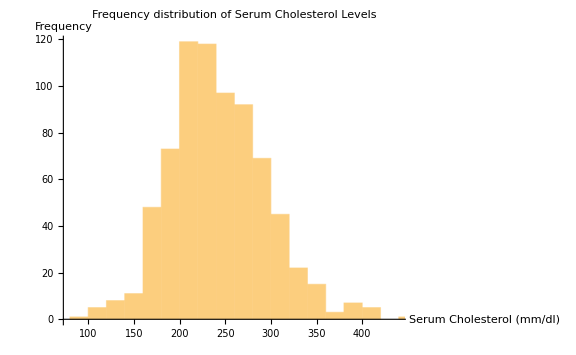

```mathematica
Histogram[Cases[lonechol, Except[0]], AxesLabel->{"Serum Cholesterol (mm/dl)","Frequency"}, ImageSize->Large, PlotLabel->"Frequency distribution of Serum Cholesterol Levels"]
```

The data looks normally distributed, when the 0 values and outliers are disregarded. However overall the data is not normally distributed

```mathematica
variablelist
```

{Age,Sex,ChestPainType,RestingBP,Cholesterol,FastingBS,RestingECG,MaxHR,ExerciseAngina,Oldpeak,ST_Slope,HeartDisease}

```mathematica
FastingBS
```

```mathematica
bstally=tally[lonebs]
```

<|0→704,1→214|>

```mathematica
GraphicsRow[{BarChart[bstally,{ChartStyle-> "Pastel", ChartLabels->Automatic, AxesLabel-> "Counts", PlotLabel->"Distribution of Blood Sugar level", LabelStyle->Directive[Bold, Thick]}],PieChart[bstally,ChartStyle->"Pastel", ChartLabels->Automatic]}]
```

-Graphics-

```mathematica
{{"0 (Blood Sugar < 120mg/ml)", PercentForm[704/(704+214)//N]},{"1 (Blood SUgar > 120mg/ml)", PercentForm[214/(704+214)//N]}}// TableForm
```

0 (Blood Sugar < 120mg/ml) | 76.69%
1 (Blood SUgar > 120mg/ml) | 23.31%

There are more patients with a serum blood sugar below 120mg/ml with 77%,  the patients with a high blood sugar level at 23% can be assumed to have diabetes, given that diabetes is a risk factor for heart disease, it would be interesting to see the relationship between heart disease diagnosis and blood sugar levels in the bi-variate analysis.

```mathematica
RestingECG
```

```mathematica
ecgtally=tally[loneecg]
```

<|Normal→552,ST→178,LVH→188|>

```mathematica
GraphicsRow[{BarChart[ecgtally,{ChartStyle-> "Pastel", ChartLabels->Automatic, AxesLabel-> "Counts", PlotLabel->"Distribution of RestingECG", LabelStyle->Directive[Bold, Thick]}], PieChart[ecgtally,ChartStyle->"Pastel", ChartLabels->Automatic]}]
```

-Graphics-

```mathematica
{{"Normal", PercentForm[552/(552+178+188)//N]},{"ST Abnormality", PercentForm[178/(552+178+188)//N]},{"LVH",PercentForm[188/(552+178+188)//N ]}}// TableForm
```

Normal | 60.13%
ST Abnormality | 19.39%
LVH | 20.48%

60% of the patients show normal ecg patterns.

```mathematica
MaxHR
```

```mathematica
lonehr//Short
```

{172,156,98,108,122,170,170,142,130,120,142,99,145,140,137,150,166,165,125,160,«878»,174,161,140,146,144,163,169,150,166,144,144,136,182,90,123,132,141,115,174,173}

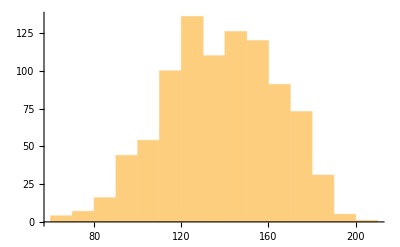

```mathematica
Histogram[lonehr]
```

```mathematica
hrnormtest =DistributionFitTest[lonehr,Automatic, "HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
hrnormtest["TestDataTable"]
```

| Statistic | P-Value
Cramér-von Mises | 0.256305 | 0.000940165

The null hypothesis that the data is distributed according to the NormalDistribution[x, y] is rejected at the 5 percent level based on the Cramér-von Mises test. Values of the MaxHR feature are not normally distributed

#### ExerciseAngina

```mathematica
angtally=tally[loneangina]
```

<|N→547,Y→371|>

```mathematica
GraphicsRow[{BarChart[angtally,{ChartStyle-> "Pastel", ChartLabels->Automatic, AxesLabel-> "Counts", PlotLabel->"Distribution of Excersise Angina", LabelStyle->Directive[Bold, Thick]}],PieChart[angtally,ChartStyle->"Pastel", ChartLabels->Automatic]}]
```

-Graphics-

More than 50% of the patients show no symptoms of heart pain during exercise.

#### Oldpeak

```mathematica
loneold//Short
```

{0,1,0,1.5,0,0,0,0,1.5,0,0,2,0,1,0,1.5,0,0,1,3,0,1,0,3,0,0,3,0,«862»,0.6,0,0,0,0.6,3,0,2,0,0,4.4,2.8,0.4,0,0,0.8,1.2,2.8,4,0,0,1,0.2,1.2,3.4,1.2,0,0}

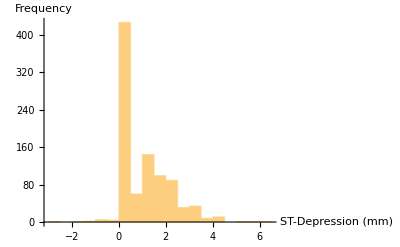

```mathematica
Histogram[loneold,AxesLabel-> {"ST-Depression (mm)","Frequency"}]
```

The distribution of oldpeak values are heavily skewed to the left to a high number of 0 values

```mathematica
oldtally =ReverseSortBy[Tally[loneold],Last] ;
```

```mathematica
Take[oldtally, 5
```

{{0,368},{1,86},{2,76},{1.5,53},{3,28}}

There are 368 , 0 values in the OldPeak variable. Indicating that majority of the patients had no st depression on the ECG.

#### ST_Slope

```mathematica
sttally =tally[lonest]
```

<|Up→395,Flat→460,Down→63|>

```mathematica
GraphicsRow[{BarChart[sttally,{ChartStyle-> "Pastel", ChartLabels->Automatic, AxesLabel-> "Counts", PlotLabel->"Distribution of ST Slope", LabelStyle->Directive[Bold, Thick]}],PieChart[sttally,ChartStyle->"Pastel", ChartLabels->Automatic]}]
```

-Graphics-

Most of the patients showed flatsloping st segment ecgs.

#### Heart Disease: How is the target variable distributed?

```mathematica
hdTally=tally[lonehd]
```

<|0→410,1→508|>

```mathematica
GraphicsRow[{BarChart[hdTally,{ChartStyle-> "Pastel", ChartLabels->Automatic, AxesLabel-> "Counts", PlotLabel->"Distribution of Heart Disease", LabelStyle->Directive[Bold, Thick]}],PieChart[hdTally,ChartStyle->"Pastel", ChartLabels->Automatic]}]
```

-Graphics-

```mathematica
{{"Negative Diagnosis", PercentForm[410/(410+508)//N]},{"Positive Diagnosis", PercentForm[508/(410+508)//N]}}// TableForm
```

Negative Diagnosis | 44.66%
Positive Diagnosis | 55.34%

The proportion of patients with a positive diagnosis is higher, however the difference is not significant enough to be considered too unbalanced for building a classifier model. This higher representation could because, an individual is more likely to consult a doctor about a heart problem if they have issues in the first place.

#### Summary of conclusions from univariate analysis

Age is not normally distributed.

Males are overrepresented in the data with approximately 79% of patients being male, with bi-variate analysis we can check how gender is distributed among diagnostic groups.

The Resting BP feature contains one outlier that shall be removed before fitting the model

MaxHR data is not normally distributed

The assumption of normal distribution is important for a lot of models including Naive Bayes and Logistic regression. Although normal distribution is not an absolute requirement, if the presence of non-normally distributed variables are negatively effecting the classifier models there is the option to have them removed or transformed to normality.

However the issue is that all the continuous data is non-normally distributed,  therefore a machine learning model that does not have the assumption of normality should be used for modelling the data.

Decision tree models do not require an assumption of normality therefore such a model will be ideal.

## Bi-Variate Analysis

Bi-variate analysis will explore the relationship between heart disease and each variable. This analysis will show if there is a significant effect of each variable on being diagnosed with heart disease.

```mathematica
The function below will automate the process of obtaining datasets and lists that contain the variable of interest for performing statistical tests and graphical representation.
```

```mathematica
variablesplit[var_, dataname_,negativename_,positivename_] := (*Function will take the variable name we need to isolate at var_, the name of the dataset with the isolated data in dataname, the name of the list containing values of from the specified column for subjects that do not have heartdisease at negativename_, and the values for all subjects that have a positive diagnosis in positivename_*)Module[{all,negvalue,posvalue}, all = GroupBy[Query[ All,{var,"HeartDisease"}] [heart2], #HeartDisease&];(*obtain all rows in dataset, and only columns that have the key HEartDisease and the desired column according to input at var, and then group them according to Value in HeartDisease, this dataset is called all*)dataname = all;(*The dataset all that was made before, is assigned to variable dataname ie. the second function argument*)negvalue= Values[all][[1]][[All,1]]// Sort;(*take values from the all dataset, this dataset is an association of a association, since its grouped by heartdisease therefore when we take Values of this nested association it gives us a nested list with two lists or teo rows, take this nested list and get the first row, that corrosponds to the group that were negatively diagnosed, then take all the rows and the 1st column from this matrix, which gives us a list containing all the variable values that we need for subjects with a negative diagnosis, asign this list to a variable that is given in the negativename argument of the function *)negativename = negvalue; posvalue= Values[all][[2]][[All,1]]// Sort;(*Same process used in the previous function for obtaining values, now for all the patients with a positive diagnosis*)positivename=posvalue;Return[dataname];
Return[negativename];Return[positivename]]
```

```mathematica
ClearAll[bivariablelist,datanamelist,negativelist,positivelist,age,sex,chest,rbp,chol,fbs,recg,hr,exa,oldp,st,age0,sex0,chest0,rbp0,fbs0,recg0,hr0,exa0,oldp0,st0,age1,sex1,chest1,rbp1,fbs1,recg1,hr1,exa1,oldp1,st1,chol0,chol1]
```

```mathematica
bivariablelist = variablelist[[;;-2]] (*List of features to be isolated, the elements are for the first argument in variablesplit function*)
```

{Age,Sex,ChestPainType,RestingBP,Cholesterol,FastingBS,RestingECG,MaxHR,ExerciseAngina,Oldpeak,ST_Slope}

```mathematica
datanamelist = {age,sex,chest,rbp,chol,fbs,recg,hr,exa,oldp,st}(*the names that will be given to the new lists containing isolated features, will form the second argument in variablesplit function *)
```

{age,sex,chest,rbp,chol,fbs,recg,hr,exa,oldp,st}

```mathematica
negativelist = {age0,sex0,chest0,rbp0, chol0,fbs0,recg0,hr0,exa0,oldp0,st0}(*Names that will be assigned to each feature, for patieents without heart disease, this will form the third argument in variablesplit function *)
```

{age0,sex0,chest0,rbp0,chol0,fbs0,recg0,hr0,exa0,oldp0,st0}

```mathematica
positivelist= {age1,sex1,chest1,rbp1,chol1,fbs1,recg1,hr1,exa1,oldp1,st1}(*Names that will be assigned to each feature, for patients with heart disease, this will form the final argument in the variablesplit function*)
```

{age1,sex1,chest1,rbp1,chol1,fbs1,recg1,hr1,exa1,oldp1,st1}

```mathematica
MapThread[variablesplit,{bivariablelist, datanamelist,negativelist,positivelist}];(*thread the varaiblesplit function over all the lists containing arguments, this will produce all the neccesary data for bi-variate analysis *)
```

The function below is for automating the tallying of all categorical variables, and creating associations of the tally lists for data visualisation and statistics.

```mathematica
categoricalclean[negative_List, positive_List,negtallyname_,postallyname_,negativeassociationname_,positiveassociationname_]:= Module[{negativetally,positivetally,negativeassociation,positiveassociation},negativetally:= Tally[negative]// Transpose;negtallyname=negativetally;positivetally:=Tally[positive]// Transpose;
postallyname=positivetally;negativeassociation:=<| "0"->AssociationThread[negativetally[[1]]-> negativetally[[2]]]|> ;negativeassociationname=negativeassociation;positiveassociation:=<| "1"->AssociationThread[positivetally[[1]]-> positivetally[[2]]]|>;positiveassociationname=positiveassociation;Return[negativetally];Return[positivetally];Return[negativeassociation];Return[positiveassociation]]
```

#### Age and Heart Disease Diagnosis

Is Age related to the presence of heart disease? We will use our data to see if there is a significant difference between the ages of patients with and without heart disease.

```mathematica
age// Short
```

age

```mathematica
age0//Short(*The ages of all the patients without heart disease*)
```

{28,29,29,29,30,31,32,32,32,33,34,34,34,34,34,35,35,35,35,35,35,35,36,36,36,36,37,«356»,65,65,66,66,66,66,66,66,67,67,67,68,68,68,68,69,69,69,70,71,71,71,72,74,74,75,76}

```mathematica
age1 // Short (*THe ages of all the patients with heart disease*)
```

{31,32,32,33,34,34,35,35,35,35,36,36,37,38,38,38,38,38,38,38,38,38,38,38,39,39,40,«455»,69,69,69,69,70,70,70,70,70,70,71,71,72,72,72,73,74,74,74,74,74,75,75,76,77,77}

```mathematica
summarymaker[n_, p_] := TableForm[{{Length[n],Length[p]},{Mean[n]//N,Mean[p]//N},{Min[n],Min[p]}, {Quantile[n, 1/4],Quantile[p,1/4]},{Quantile[n, 1/2],Quantile[p,1/2]},{Quantile[n, 3/4],Quantile[p,3/4]},{Max[n],Max[p]}}, TableHeadings-> {{"Count","Mean","Min","25% Quantile","50% Quantile (Median)", "75% Quantile","Max"},{"Negative","Positive"}}]
```

```mathematica
summarymaker[age0,age1]
```

| Negative | Positive
Count | 410 | 508
Mean | 50.5512 | 55.8996
Min | 28 | 31
25% Quantile | 43 | 51
50% Quantile (Median) | 51 | 57
75% Quantile | 57 | 62
Max | 76 | 77

```mathematica
whisviol[n_,p_]:= Column[{Row[{BoxWhiskerChart[{n,p}, {"Outliers",{"MedianMarker",1,Directive[Thick,Red]}} ,ChartStyle->ColorData[97,"ColorList"][[1;;2]], ImageSize->Medium],DistributionChart[{n,p},ChartStyle->ColorData[97,"ColorList"][[1;;2]], ImageSize->Medium]}],PointLegend[ColorData[97,"ColorList"][[1;;2]],{0,1},LegendLayout->"Row",LegendMarkers->{Automatic, Small},LegendFunction->"Frame",LegendLabel->"Heart Disease"]},Alignment->Center] (*This function takes as the first argument the list containg continous values in diagnostic class 0 as a first argument and, as last argument values from diagnostic class1 , and produces a Box whisker chart and a violin plot*)
```

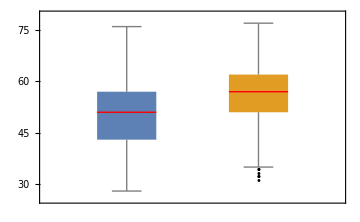
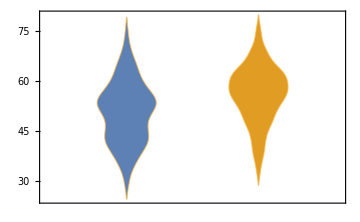

```mathematica
whisviol[age0,age1]
```

According to this plot there are some outliers among the group with heart disease,  these outliers represent individuals of a young age that have developed Heart disease , which is a rare occurrence.

I will check if Age has a significant effect on heart disease using a t-test, a T-test is a statistical test that is used determine if there is a statistically significant difference in the means of a dependant variable between two populations. If there is a significant difference in the means of the age between the two groups (heart disease 0 or 1) this means that age has a significant effect on heart disease, A T-test requires assumptions, one is the normal distribution of the data, and the other is the homogeneity of the variance or that the variances of the two groups must be similar. The age data do not follow a normal distribution as we saw in the uni-variate analysis.

```mathematica
VarianceEquivalenceTest[{age0,age1},"TestDataTable"](*The data does not meet the assumption for homogeneity of variance*)
```

| Statistic | P-Value
Conover | 2.64608 | 0.00814303

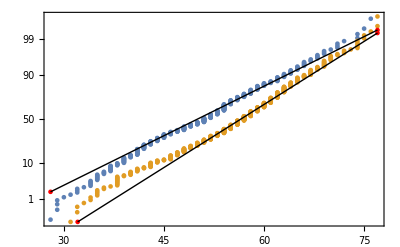

```mathematica
ProbabilityScalePlot[{age0,age1},"Normal", ReferenceLineStyle->Directive[Dashing[{}],Red]] (*When the age data is split according to diagnostic class, the plot shows that the data is normally distributed because the plotted points adhere closely to the red line that displays the refence line for normally distributed data*)
```

```mathematica
{DistributionFitTest[age0,Automatic,{"TestDataTable", "AndersonDarling"}],DistributionFitTest[age1,Automatic,{"TestDataTable","AndersonDarling"}]} (*However the test for normality says that both populations are not normaly distributed*)
```

{ | Statistic | P-Value
Anderson-Darling | 0.91397 | 0.0191535, | Statistic | P-Value
Anderson-Darling | 2.49966 | 0.}

Because the assumptions for t-test in terms of homogeneity of variance and normality are not met, a Mann-WHitney U test will be carried, a non-parametric test that does not require an assumption of normality or homogeneity of variance

Mann-Whitney U test:
Null Hypothesis (H0) : there is no significant difference in the median age between patients diagnosed with and without heart disease 
Alternative Hypothesis (Ha) : There is a significant difference in medians

```mathematica
MannWhitneyTest[{age0,age1},Automatic, {"TestDataTable","HypothesisTestData"}]
```

{ | Statistic | P-Value
Mann-Whitney | 69137.5 | 1.80569×10^-18,HypothesisTestData[…]}

The null hypothesis that the median difference is 0 is rejected at the 5 percent level based on the Mann-Whitney test. There is a statistically significant difference between the median age of patients with and without heart disease , the median Age of patients with heart disease is higher.

This data shows that the prevalence  of heart disease is higher in older patients.

#### Gender and Heart Disease

```mathematica
sex//Short
```

<|0→{<|Sex→M,HeartDisease→0|>,<|Sex→M,HeartDisease→0|>,«406»,<|Sex→M,HeartDisease→0|>,<|Sex→M,HeartDisease→0|>},1→{<|Sex→F,Hea…ase→1|>,«507»}|>

```mathematica
sex0//Short
```

{F,F,F,F,F,F,F,F,F,F,F,F,F,F,F,F,F,F,F,F,«370»,M,M,M,M,M,M,M,M,M,M,M,M,M,M,M,M,M,M,M,M}

```mathematica
sex1 //Short
```

{F,F,F,F,F,F,F,F,F,F,F,F,F,F,F,F,F,F,F,F,«468»,M,M,M,M,M,M,M,M,M,M,M,M,M,M,M,M,M,M,M,M}

```mathematica
ClearAll[s0t,s1t,s0ta,s1ta]
```

```mathematica
categoricalclean[sex0,sex1,s0t,s1t,s0ta,s1ta]
```

{{F,M},{143,267}}

```mathematica
s0t
```

{{F,M},{143,267}}

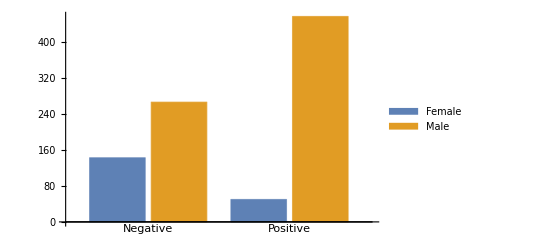

```mathematica
BarChart[<|s0ta,s1ta|>, ChartStyle-> 97,ChartLegends->{"Female","Male"}, ChartLabels->{{"Negative","Positive"},None}]
```

pieoven[d_Association,hd_String,c_List] function is for calculating the percentage of each class and outputting a pie chart.

```mathematica
pieoven[d_Association,hd_String,c_List]:= Module[{a,b,e,isolatedata,calculated,pie}, 
fp[g_,t_]:=g/t ; 
a=Table[d,{Range[Length[c]]}];
isolate[x_Association,w_String,v_]:= x[w][v];(**)
 b =Table[hd,{Range[Length[c]]}];
isolatedata = MapThread[isolate,{a,b,c}];
If[hd== "0",e= Table[410,{Range[Length[c]]}],e= Table[508,{Range[Length[c]]}]]; 
calculated =N[MapThread[fp,{isolatedata, e}],2];
label = If[hd =="0", label = "Negative", label ="Positive"];
pie = PieChart[calculated, ChartLabels->Placed[PercentForm /@calculated,"RadialCallout"], ChartStyle-> 97,PlotLabel->label, LabelStyle->Directive[Bold, Thick]];Return[pie]]
```

```mathematica
sexpie0 =pieoven[s0ta,"0",{"F","M"}];
```

```mathematica
sexpie1 = pieoven[s1ta, "1", {"F","M"}];
```

```mathematica
piewarmer[n_,p_, v_List,f_String] := Column[{Row[{n,p}],PointLegend[ColorData[97,"ColorList"],v,LegendLayout->"Row",LegendMarkers->{Square, Medium},LegendFunction->"Frame",LegendLabel->f]},Alignment->Center]
```

```mathematica
piewarmer[sexpie0,sexpie1, {"Female","Male"},"Sex"]
```

-Graphics--Graphics-

More men are represented percentage wise in the positive group, a heart disease patient has a 90% likelihood being male, while there is only a 9.8% likelihood of a heart disease patient being female. However, there are more men represented in both groups this could be a reflection of there being more males in the dataset.

If males are represented more in the positive group, due to a bias in the sex ratio of the data, this would present problems for the model. Considering the proportional representation of sick individuals in each gender group would help us understand if the pattern we see is natural or due to bias in the data.

```mathematica
GraphicsRow[{PieChart[{s0ta["0"]["F"]/(s0ta["0"]["F"]+s1ta["1"]["F"])//N,s1ta["1"]["F"]/(s0ta["0"]["F"]+s1ta["1"]["F"])//N}, ChartLabels->Placed[{PercentForm[s0ta["0"]["F"]/(s0ta["0"]["F"]+s1ta["1"]["F"])//N],PercentForm[s1ta["1"]["F"]/(s0ta["0"]["F"]+s1ta["1"]["F"])//N]},"RadialCallout"], ChartLegends->{"0","1"}, PlotLabel-> "Female", LabelStyle->Directive[Bold, Thick], ImageSize->Large], PieChart[{s0ta["0"]["M"]/(s0ta["0"]["M"]+s1ta["1"]["M"])//N,s1ta["1"]["M"]/(s0ta["0"]["M"]+s1ta["1"]["M"])//N},ChartLabels->Placed[{PercentForm[s0ta["0"]["M"]/(s0ta["0"]["M"]+s1ta["1"]["M"])//N],PercentForm[s1ta["1"]["M"]/(s0ta["0"]["M"]+s1ta["1"]["M"])//N]}, "RadialCallout"],ChartLegends->{"0","1"}, PlotLabel-> "Male", LabelStyle->Directive[Bold, Thick], ImageSize -> Large]}, Spacings-> 0, ImageSize->Full]
```

-Graphics-

Analysing the data by grouping into gender also reveals that males are more likely to have heart disease, with a 63% of a male patient being positively diagnosed, compared to 25.9% in female patients. Therefore, it is likely that the greater proportion of males found in the positive diagnosis group is not due to a skew in the distribution of genders overall.

To increase the certainty of this observation a statistical test will be carried out.

Both the Independent variable and the dependant variable are categorical, for such cases the statistical test that is normally used is a Chi-Squared Test (χ2 test).The Chi-Squared test is a hypothesis test that assumes the null hypothesis that the observed frequencies for a categorical dependant variable match the expected frequencies for the categorical  independent variable. The test calculates a statistic that has a chi-squared distribution.
-Graphics- A Chi Squared distribution [https://www.sciencedirect.com/topics/mathematics/chi-square-distribution]
Given the Sex/diagnosis example above, the number of observations for a category (such as male and female) may or may not the same. Nevertheless, we can calculate the expected frequency of observations in each diagnosis group and see whether the partitioning of diagnosis by Sex results in similar or different frequencies.

The Chi-Squared test does this for a contingency table, first calculating the expected frequencies for the groups, then determining whether the division of the groups, called the observed frequencies, matches the expected frequencies.

The result of the test is a test statistic that has a chi-squared distribution and can be interpreted to reject or fail to reject the assumption or null hypothesis that the observed and expected frequencies are the same. The Alternative Hypothesis is that the observed and expected frequencies are different, if they are different it means that one of the sexes is disproportionately represented in one diagnostic group.

```mathematica
(*Mathematica does not have an inbuilt function for Chi Squared goodness of fit test, so have to construct unique function, I am trying to replicate this equation -Graphics-, where observed is the actual frequency of a variable in the data, and  expected is the frequency expected according to a chi squared distribution, then sum up the ratio for each independant variable (with or without heart disease) and this sum is the chi squared test statistic, the test statstic number and the degrees of freedom then inform us of what the p-value is, again if the p-value is greater than 0.05 then the differences between groups are statistically significant.*)(*This code is adopted from stackexchange: https://mathematica.stackexchange.com/questions/5271/doing-a-chi-square-independence-test-in-mathematica/5285#5285https://mathematica.stackexchange.com/questions/5271/doing-a-chi-square-independence-test-in-mathematica/5285#5285Nonehttps://mathematica.stackexchange.com/questions/5271/doing-a-chi-square-independence-test-in-mathematica/5285#5285HyperlinkActionRecycledHyperlinkActive*)
```

```mathematica
Print[TableForm[{{"Male Negative (MN)","Male Positive (MP)", "Male Total (ΣM) "},{"Female Negative (FN)","Female Postive (FP)","Female Positive (ΣFP)"}, {"Negative Total (ΣN)","Postive Total (ΣP)", "Overall Total (Overall)"}}, TableHeadings->{{"Male","Female"},{"Negative diagnosis", "Positive Diagnosis"}}], "   This Table contains all the observed values from the data we have"]
Print[TableForm[{{"(ΣN * ΣM)/ Overall, (EMN)","(ΣP * ΣM)/ Overall, (EMP)"},{"(ΣN * ΣF)/ Overall, (EFN)","(ΣP * ΣF)/Overall, (EFP)"}}, TableHeadings->{{"Male","Female"},{"Negative diagnosis", "Positive Diagnosis"}}], "                 This table contains all the expected values if the data followed a Chi squared distribution"]
Print[TableForm[{{"(MN-EMN)"," (MP-EMP)"},{"(FN-EFN)","(FP-EFP)"}}, , TableHeadings->{{"Residuals","Residuals"}}],"                                              Calculating the residuals when we subtract the expected values from observed"]
Print[TableForm[{{"(MN-EMN)^2"," (MP-EMP)^2"},{"(FN-EFN)^2","(FP-EFP)^2"}}, , TableHeadings->{{"Residuals^2"},{"Residuals^2"}}],"                                     Squaring the residuals"]
Print["Chi-Squared statistic(χ2)= (MN-EMN)^2 + (MP-EMP)^2 + (FN-EFN)^2 + (FP-EFP)^2 "]
Print["Degrees of Freedom(df)= (Number of rows -1)(Number of Columns -1) "]
```

| Negative diagnosis | Positive Diagnosis | 
Male | Male Negative (MN) | Male Positive (MP) | Male Total (ΣM) 
Female | Female Negative (FN) | Female Postive (FP) | Female Positive (ΣFP)
 | Negative Total (ΣN) | Postive Total (ΣP) | Overall Total (Overall)   This Table contains all the observed values from the data we have

| Negative diagnosis | Positive Diagnosis
Male | (ΣN * ΣM)/ Overall, (EMN) | (ΣP * ΣM)/ Overall, (EMP)
Female | (ΣN * ΣF)/ Overall, (EFN) | (ΣP * ΣF)/Overall, (EFP)                 This table contains all the expected values if the data followed a Chi squared distribution

Residuals | (MN-EMN) |  (MP-EMP)
Residuals | (FN-EFN) | (FP-EFP)                                              Calculating the residuals when we subtract the expected values from observed

| Residuals^2 | 
Residuals^2 | (MN-EMN)^2 |  (MP-EMP)^2
 | (FN-EFN)^2 | (FP-EFP)^2                                     Squaring the residuals

Chi-Squared statistic(χ2)= (MN-EMN)^2 + (MP-EMP)^2 + (FN-EFN)^2 + (FP-EFP)^2

Degrees of Freedom(df)= (Number of rows -1)(Number of Columns -1)

```mathematica
data={s0t[[2]],s1t[[2]]}// Transpose (*These are the tally totals for each category, {{Male without, Male With},{Female without, Male With}}*)
rc={{"male","female"},{"negative","positive"}};
TableForm[data,TableHeadings->rc] (*THis will form a contingancy table for calculating the test statistic, using the tableheading in rc and the data, showing the observed frequencies for each group*)
fit=Outer[Times,Total[data,{2}],Total[data]]/Total[data,2]; (*For calcualting the expected values if the groups were indpendant and the numbers were random, they follow the formula *)
TableForm[fit//N,TableHeadings->rc] (*for making a table displaying the expected frequencies according to CHi squared distributioj*)
residual=data-fit; (*The residuals or the observed values minus the expected values*)
TableForm[residual//N,TableHeadings->rc](*Table of residuals*)
χ2array=residual^2/fit; (*Square the residuals and divide by expected values to rescale according reciprocal of expected value ((observed-expected)^2)/ expected) *)
TableForm[χ2array//N,TableHeadings->rc] (*Make table of rescaled and squared residuals  *)
χ2=Total[χ2array,2];  (*Sum of scaled residuals this gives us the CHi squared test statistic*)
χ2//N
df=(Times@@#-Total[#]+1)&[Dimensions[data]]; (*This is for calcualting the degrees of freedom which is necessary for determining the p-value needed for hypothesis testing*)
N[1-CDF[ChiSquareDistribution[df],χ2],3](*The p-value.This assesses the chance that a chi-squared random variable could attain a value of 𝜒2 or larger.*)
```

{{267,50},{143,458}}

| negative | positive
male | 267 | 50
female | 143 | 458

| negative | positive
male | 141.58 | 175.42
female | 268.42 | 332.58

| negative | positive
male | 125.42 | -125.42
female | -125.42 | 125.42

| negative | positive
male | 111.106 | 89.672
female | 58.6032 | 47.2979

306.679

1.16×10^-68

```mathematica
(*The p-value is substantially less than the significance threshold of p=0.05 , therefore the null hypothesis can be rejected , indicating that there is significantly more males affected by heart disease than females.*)
```

The Chi- Squared test can conform that the disparity in heart disease among the two sexes is statistically significant, and not likely to be a result of the skewed distribution in the data.

#### ChestPainType and Heart Disease

```mathematica
chest//Short
```

<|0→{<|ChestPainType→ATA,HeartDisease→0|>,<|ChestPainType→ATA,HeartDisease→0|>,«407»,<|ChestPainType→NAP,HeartDisease→0|>},1→{«1»}|>

```mathematica
ClearAll[cpt0t,cpt1t,cpt0ta,cpt1ta]
```

```mathematica
categoricalclean[chest0,chest1,cpt0t,cpt1t,cpt0ta,cpt1ta](*cpt0t is a tally of chest pain types for negative patients,cpt1t is a tally of chest pain types for positive pations, cpt0ta and cot1ta are associations of the tally lists *)
```

{{ASY,ATA,NAP,TA},{104,149,131,26}}

```mathematica
cpt0t
```

{{ASY,ATA,NAP,TA},{104,149,131,26}}

```mathematica
cpt1t
```

{{ASY,ATA,NAP,TA},{392,24,72,20}}

```mathematica
cpt0ta
```

<|0→<|ASY→104,ATA→149,NAP→131,TA→26|>|>

```mathematica
cpt0ta
```

{{ASY,ATA,NAP,TA},{104,149,131,26}}

```mathematica
flip[tally0_,tally1_]:= Module[{nest,final}, nest = {tally0,tally1}//Transpose;Return[nest[[2]]//Transpose]] (*This funcion will flip the varaible why which data is gathered for cases where I want to illustarate the presence or absense of heart disease for a variable*)
```

```mathematica
chestflip=flip[cpt0t,cpt1t](*Gathering according to chest pain type to see how each group with chest pain type is diagnosed*)
```

{{104,392},{149,24},{131,72},{26,20}}

```mathematica
GraphicsRow[{BarChart[<|cpt0ta,cpt1ta|>,ChartStyle->97, ChartLegends->{"ASY","ATA","NAP","TA"}, ChartLabels->{{"Negative","Positive"},None},PlotLabel->"Distrbution of Angina types in diagnostic classes", ImageSize->Large], BarChart[chestflip,ChartLegends->{"0","1"}, PlotLabel->"Distribution of diagnostic classes for Angina Types",ChartLabels->{{"ASY","ATA","NAP","TA"},None}, ImageSize->Large]}, ImageSize->Full]
```

-Graphics-

```mathematica
cptclist = cpt0t[[1]]
```

{ASY,ATA,NAP,TA}

```mathematica
painpie0 =pieoven[cpt0ta,"0",cptclist];
```

```mathematica
painpie1 = pieoven[cpt1ta,"1",cptclist];
```

```mathematica
piewarmer[painpie0,painpie1, cptclist,"Chest Pain Type"]
```

-Graphics--Graphics-

77% of patients with heart disease showed no symptoms of Angina (asymptomatic), and the majority of patients who are asymptomatic have heart disease.  This illustrates the difficulty in diagnosing heart disease, heart pain one of the most well known symptoms of heart disease do not manifest themselves in patients.

The second most common form of chest pain in patients with heart disease is non anginal pain, this is heart pain that cannot be linked to cardiac causes, such as heartburn. Such symptoms are quite common in populations and usually not linked to heart disease. However here we can see a clear majority of people with non anginal pain having heart disease.

The majority of people with atypical angina, do not have heart disease.

### RestingBP and HeartDisease

```mathematica
rbp// Short
```

<|0→{<|RestingBP→140,HeartDisease→0|>,<|RestingBP→130,HeartDisease→0|>,«406»,<|RestingBP→120,HeartDisease→0|>,<|RestingBP→138,HeartDisease→0|>},1→{«1»}|>

```mathematica
rbp0// Short
```

{80,94,94,98,100,100,100,100,100,100,100,100,101,102,102,104,104,105,105,105,«370»,160,160,160,160,160,160,160,160,170,170,170,172,178,180,180,180,180,180,180,190}

```mathematica
rbp1//Short
```

{0,92,95,95,95,95,95,95,96,100,100,100,100,100,100,100,102,104,105,105,105,«466»,170,170,170,170,172,174,178,178,180,180,180,180,180,180,185,190,192,200,200,200,200}

```mathematica
summarymaker[rbp0,rbp1]
```

| Negative | Positive
Count | 410 | 508
Mean | 130.18 | 134.185
Min | 80 | 0
25% Quantile | 120 | 120
50% Quantile (Median) | 130 | 132
75% Quantile | 140 | 145
Max | 190 | 200

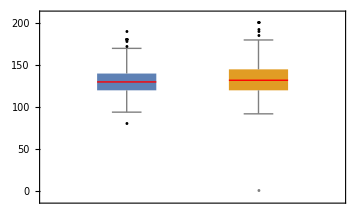
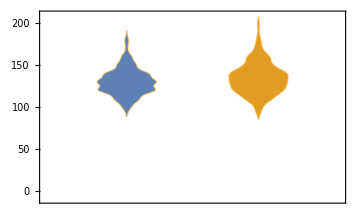

```mathematica
whisviol[rbp0,rbp1]
```

The distribution of resting blood pressure appears to be similar between the two groups, the outlier at value 0 is found within the group with heart disease, this row will be removed in the final model .

#### Cholesterol and Heart Disease

```mathematica
chol// Short
```

<|0→{<|Cholesterol→289,HeartDisease→0|>,<|Cholesterol→283,HeartDisease→0|>,«406»,<|Cholesterol→157,HeartDisease→0|>,<|Cholesterol→175,HeartDisease→0|>},1→«1»|>

```mathematica
chol0//Short
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,85,100,126,129,132,«360»,320,320,321,325,325,326,328,339,340,340,342,344,347,354,358,360,365,385,394,394,412,417,458,468,564}

```mathematica
chol1// Short
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«456»,335,336,337,338,339,341,341,341,342,342,349,353,355,369,384,388,392,393,404,407,409,466,491,518,529,603}

```mathematica
summarymaker[chol0,chol1]
```

| Negative | Positive
Count | 410 | 508
Mean | 227.122 | 175.941
Min | 0 | 0
25% Quantile | 197 | 0
50% Quantile (Median) | 227 | 217
75% Quantile | 267 | 267
Max | 564 | 603

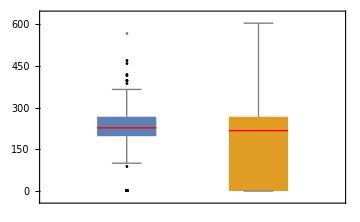
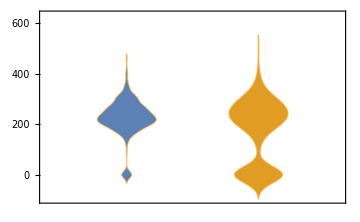

```mathematica
whisviol[chol0,chol1]
```

There are several outliers in the group without heart disease, the maximum is 500, this is a severe level of cholesterol, this individual is at severe risk of heart attack, however is diagnosed with no heart disease, this is quite interesting. The mean marker is in red, while the median marker is white, the median appears to be similar while the mean is different. Curiously the mean for people heart disease is lower, it should be the other way around, The distribution chart will show us why this could be the case.

There are two main clusters in the positive diagnosis group, one that is very low and mainly consisting of 0, this is what is dragging the mean down to be below the negative diagnosis group, it is likely that all these 0 values are simply missing values that were replaced in the dataset. The main “body” of cholesterol levels in the positive and negative groups are similar in magnitude

Given the high number of people with a cholesterol level of 0 (172) as we discovered in the uni-variate visualizations, it would be helpful to visualise how these 0 values are distributed according to diagnostic group.

```mathematica
cholzero=Cases[chol, <| "Cholesterol"-> 0,___|>, {2}]; (*All the rows with 0 cholesterol level*)
```

```mathematica
cholzero=GroupBy[cholzero, #HeartDisease&];
```

```mathematica
<|"0"->Flatten[Tally[cholzero[[1]]]][[-1]]|>
```

<|0→20|>

```mathematica
<| "1"->Flatten[Tally[cholzero[[2]]]][[-1]]|>
```

<|1→152|>

```mathematica
GraphicsRow[{BarChart[<|<|"0"->Flatten[Tally[cholzero[[1]]]][[-1]]|>,<| "1"->Flatten[Tally[cholzero[[2]]]][[-1]]|>|>, ChartStyle->82, ChartLabels->{"0","1"},ChartLegends->{"0","1"},ImageSize->Medium],PieChart[{<|<|"0"->Flatten[Tally[cholzero[[1]]]][[-1]]|>,<| "1"->Flatten[Tally[cholzero[[2]]]][[-1]]|>|>},ChartLabels->Placed[PercentForm /@{N[20/172],N[152/172]},"RadialCallout"], ChartStyle->82,ChartLegends->{"0","1"},ImageSize-> Medium]},ImageSize->Full]
```

88.37% of the people with 0 cholesterol has heart disease in this dataset. This statistic along with the violin plot  showing the similarity in distribution of cholesterol levels between the two diagnostic groups, show that high cholesterol cannot be linked to likelihood of having heart disease.

#### Fasting Blood Sugar and Heart Disease

```mathematica
fbs // Short
```

<|0→{<|FastingBS→0,HeartDisease→0|>,<|FastingBS→0,HeartDisease→0|>,«406»,<|FastingBS→0,HeartDisease→0|>,<|FastingBS→0,HeartDisease→0|>},1→{«1»}|>

```mathematica
fbs0 // Short
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«330»,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
fbs1 // Short
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«428»,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
ClearAll[fbs0t,fbs1t,fbs0ta,fbs1ta]
```

```mathematica
categoricalclean[fbs0,fbs1,fbs0t,fbs1t,fbs0ta,fbs1ta]
```

{{0,1},{366,44}}

```mathematica
fbs0t =
```

{{0,1},{366,44}}

```mathematica
fbs1t
```

{{0,1},{338,170}}

```mathematica
fbs0ta
```

<|0→<|0→366,1→44|>|>

```mathematica
fbs1ta
```

<|1→<|0→338,1→170|>|>

```mathematica
bloodflip=flip[fbs0t,fbs1t]
```

{{366,338},{44,170}}

```mathematica
GraphicsRow[{BarChart[<|fbs0ta,fbs1ta|>, ChartStyle->97,ChartLegends->{"Normal", "High Blood Sugar (>120mg/ml)"},PlotLabel->"Distribution of Fasting BS in diagnostic classes", ChartLabels->{{"Negative","Positive"},None}, ImageSize->Medium],BarChart[bloodflip, ChartLabels->{{"Normal","High"},None},PlotLabel->"Distribution of Diagnostic classes in Fasting BS", ChartLegends->{"0","1"},ImageSize-> Medium]}, ImageSize->Full]
```

-Graphics-

```mathematica
fbsvalist = fbs0t[[1]]
```

{0,1}

```mathematica
fbs0ta["0"][0]
```

366

```mathematica
sugarpie0 =pieoven[fbs0ta,"0", {0,1}];
```

```mathematica
sugarpie1 =pieoven[fbs1ta,"1", fbsvalist];
```

```mathematica
piewarmer[sugarpie0,sugarpie1, {"Normal","High Blood Sugar"}, "High Blood Sugar"]
```

-Graphics--Graphics-

33% of patients with heart disease have a blood sugar level higher than 120 mg/dl, indicating presence of Type II diabetes. While 67% had no diabetes .

The majority of patients with normal blood sugar did not have heart disease, but a significant number did.

The majority of patients with high blood sugar were diagnosed with heart disease.  This is to be expected since diabetes is considered to be a risk factor for heart disease.

#### RestingECG and Heart Disease

```mathematica
variablelist
```

{Age,Sex,ChestPainType,RestingBP,Cholesterol,FastingBS,RestingECG,MaxHR,ExerciseAngina,Oldpeak,ST_Slope,HeartDisease}

```mathematica
recg//Short
```

<|0→{<|RestingECG→Normal,HeartDisease→0|>,<|RestingECG→ST,HeartDisease→0|>,«407»,<|RestingECG→Normal,HeartDisease→0|>},1→{«1»}|>

```mathematica
recg0//Short
```

{LVH,LVH,LVH,LVH,LVH,LVH,LVH,LVH,LVH,LVH,LVH,LVH,LVH,LVH,«382»,ST,ST,ST,ST,ST,ST,ST,ST,ST,ST,ST,ST,ST,ST}

```mathematica
recg1//Short
```

{LVH,LVH,LVH,LVH,LVH,LVH,LVH,LVH,LVH,LVH,LVH,LVH,LVH,LVH,«480»,ST,ST,ST,ST,ST,ST,ST,ST,ST,ST,ST,ST,ST,ST}

```mathematica
ClearAll[recg0t,recg1t,recg0ta,recg1ta]
```

```mathematica
categoricalclean[recg0,recg1,recg0t,recg1t,recg0ta,recg1ta]
```

{{LVH,Normal,ST},{82,267,61}}

```mathematica
recg0t
```

{{LVH,Normal,ST},{82,267,61}}

```mathematica
recg1t
```

{{LVH,Normal,ST},{106,285,117}}

```mathematica
recg0ta
```

<|0→<|LVH→82,Normal→267,ST→61|>|>

```mathematica
recg1ta
```

<|1→<|LVH→106,Normal→285,ST→117|>|>

```mathematica
ecgflip=flip[recg0t,recg1t]
```

{{82,106},{267,285},{61,117}}

```mathematica
GraphicsRow[{BarChart[<|recg0ta,recg1ta|>,ChartStyle->97 ,ChartLegends->{"Normal", "ST-Wave abnormality","Left ventricular hypertrophy"}, ChartLabels->{{"Negative","Positive"},None},PlotLabel->"Distribution of RestingECG according to diagnostic class", ImageSize->Medium],BarChart[ecgflip, ChartLabels->{{"LVH","Normal","ST"},None}, ChartLegends->{0,1},PlotLabel->"Distribution of diagnostic class in Resting ECG", ImageSize->Medium]},ImageSize->Full]
```

-Graphics-

```mathematica
ecgpie0=pieoven[recg0ta,"0",{"LVH","Normal","ST"}];
```

```mathematica
ecgpie1 = pieoven[recg1ta,"1",{"LVH","Normal","ST"}];
```

```mathematica
piewarmer[ecgpie0,ecgpie1,{"LVH","Normal","ST"}, "Resting ECG" ]
```

-Graphics--Graphics-

Positive patients have more st wave abnormality and left ventricular hypertrophy, this is to be expected, what is interesting is that a greater proportion of patients with heart disease have normal ECG waves (56%), this makes diagnosis harder.

Out of patients with normal ECG charts , a majority were diagnosed with heart disease.

#### MaxHR and Heart Disease

```mathematica
hr // Short
```

<|0→{<|MaxHR→172,HeartDisease→0|>,<|MaxHR→98,HeartDisease→0|>,«406»,<|MaxHR→182,HeartDisease→0|>,<|MaxHR→173,HeartDisease→0|>},1→{«1»}|>

```mathematica
hr0 //Short
```

{69,80,86,86,90,96,96,96,97,98,98,99,100,100,100,100,100,100,105,106,107,«368»,182,182,182,184,184,184,184,185,185,185,185,186,186,187,188,188,190,190,192,194,202}

```mathematica
hr1 // Short
```

{60,63,67,70,71,72,72,73,77,78,80,82,82,82,83,84,84,84,86,86,87,88,88,«463»,170,170,170,170,170,170,171,173,173,174,174,175,175,175,176,177,180,180,181,182,182,195}

```mathematica
variablelist
```

{Age,Sex,ChestPainType,RestingBP,Cholesterol,FastingBS,RestingECG,MaxHR,ExerciseAngina,Oldpeak,ST_Slope,HeartDisease}

```mathematica
summarymaker[hr0,hr1]
```

| Negative | Positive
Count | 410 | 508
Mean | 148.151 | 127.656
Min | 69 | 60
25% Quantile | 134 | 112
50% Quantile (Median) | 150 | 126
75% Quantile | 165 | 144
Max | 202 | 195

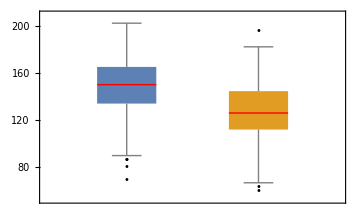
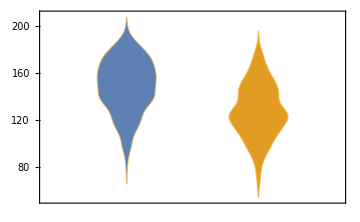

```mathematica
whisviol[hr0,hr1]
```

```mathematica
variablelist
```

{Age,Sex,ChestPainType,RestingBP,Cholesterol,FastingBS,RestingECG,MaxHR,ExerciseAngina,Oldpeak,ST_Slope,HeartDisease}

Mann-Whitney U test:
Null Hypothesis (H0) : there is no significant difference in the median maxHR between patients diagnosed with and without heart disease 
Alternative Hypothesis (Ha) : There is a significant difference in medians

```mathematica
MannWhitneyTest[{hr0,hr1},Automatic, {"TestDataTable","HypothesisTestData"}]
```

{ | Statistic | P-Value
Mann-Whitney | 153090. | 1.50171×10^-34,HypothesisTestData[…]}

The null hypothesis that the median difference is 0 is rejected at the 5 percent level based on the Mann-Whitney test. There is a statistically significant difference between the median MaxHR of patients with and without heart disease . The median of the maximum heart rate is lower in patients with heart disease

#### ExerciseAngina and Heart Disease

```mathematica
exa//Short
```

<|0→{<|ExerciseAngina→N,HeartDisease→0|>,<|ExerciseAngina→N,HeartDisease→0|>,«407»,<|ExerciseAngina→N,HeartDisease→0|>},1→{<|ExerciseAngina→N,H…e→1|>,«507»}|>

```mathematica
exa0 // Short
```

{N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,«370»,Y,Y,Y,Y,Y,Y,Y,Y,Y,Y,Y,Y,Y,Y,Y,Y,Y,Y,Y,Y}

```mathematica
exa1// Short
```

{N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,N,«468»,Y,Y,Y,Y,Y,Y,Y,Y,Y,Y,Y,Y,Y,Y,Y,Y,Y,Y,Y,Y}

```mathematica
ClearAll[exa0t,exa1t,exa0ta,exa1ta]
```

```mathematica
categoricalclean[exa0,exa1,exa0t,exa1t,exa0ta,exa1ta]
```

{{N,Y},{355,55}}

```mathematica
exa0t
```

{{0,1},{355,55}}

```mathematica
exa1t
```

{{0,1},{192,316}}

```mathematica
exa0ta
```

<|0→<|0→355,1→55|>|>

```mathematica
exa1ta
```

<|1→<|0→192,1→316|>|>

```mathematica
exaflip = flip[exa0t,exa1t]
```

{{355,192},{55,316}}

```mathematica
GraphicsRow[{BarChart[<|exa0ta,exa1ta|>, ChartStyle->97,ChartLegends->{"No Exercise Angina", "Exercise Angina present"}, ChartLabels->{{"Negative","Positive"},None}, ImageSize->Medium], BarChart[exaflip, ChartLabels->{{"0","1"},None}, ChartLegends->{0,1}, ImageSize-> Medium]},ImageSize->Full]
```

-Graphics-

```mathematica
exa0t
```

{{N,Y},{355,55}}

```mathematica
pieoven[d_Association,hd_String,c_List]:= Module[{a,b,e,isolatedata,calculated,pie}, 
fp[g_,t_]:=g/t ; 
a=Table[d,{Range[Length[c]]}];
isolate[x_Association,w_String,v_]:= x[w][v];(**)
 b =Table[hd,{Range[Length[c]]}];
isolatedata = MapThread[isolate,{a,b,c}];
If[hd== "0",e= Table[410,{Range[Length[c]]}],e= Table[508,{Range[Length[c]]}]]; 
calculated =N[MapThread[fp,{isolatedata, e}],2];
label = If[hd =="0", label = "Negative", label ="Positive"];
pie = PieChart[calculated, ChartLabels->Placed[PercentForm /@calculated,"RadialCallout"], PlotLabel->label, LabelStyle->Directive[Bold, Thick]];Return[pie]]
```

```mathematica
exercisepie0 =pieoven[exa0ta,"0",{"N","Y"}];
```

```mathematica
exercisepie1 = pieoven[exa1ta, "1",{"N","Y"}];
```

```mathematica
piewarmer[exercisepie0,exercisepie1, {"0","1"}, "Excercise Angina"]
```

-Graphics--Graphics-

The number of heart disease positive patients with exercise angina is high, however the number not presenting this symptom is also quite high, with over 192 (>50%)not having exercise angina, given that exercise induced chest pain is a common diagnostic factor, this result shows again how difficult it is to diagnose heart disease

#### Oldpeak and Heart Disease

```mathematica
oldp// Short
```

<|0→{<|Oldpeak→0,HeartDisease→0|>,<|Oldpeak→0,HeartDisease→0|>,«406»,<|Oldpeak→0,HeartDisease→0|>,<|Oldpeak→0,HeartDisease→0|>},1→{«1»}|>

```mathematica
oldp0// Short
```

{-1.1,-0.5,-0.1,-0.1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«354»,1.8,1.8,1.8,1.9,1.9,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2.3,2.3,2.4,2.6,3,3,3,3.5,4.2}

```mathematica
oldp1 // Short
```

{-2.6,-2,-1.5,-1,-1,-0.9,-0.8,-0.7,-0.5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«463»,3.4,3.4,3.5,3.6,3.6,3.6,3.6,3.7,3.8,4,4,4,4,4,4,4,4,4.2,4.4,5,5.6,6.2}

```mathematica
summarymaker[oldp0,oldp1]
```

| Negative | Positive
Count | 410 | 508
Mean | 0.408049 | 1.27421
Min | -1.1 | -2.6
25% Quantile | 0 | 0
50% Quantile (Median) | 0 | 1.2
75% Quantile | 0.6 | 2
Max | 4.2 | 6.2

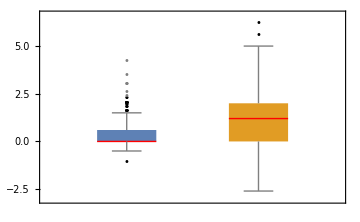
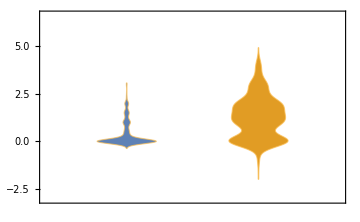

```mathematica
whisviol[oldp0,oldp1]
```

The st depression for the group with no heart disease is lower, with mean and median around 0 as expected, however there are a lot of outliers that go to maximum of 4.2 mm, this is atypical, however a high st depression is not necessarily an indicator of heart disease, there are other courses for st depression . Again this shows the difficulty in diagnosing heart disease .

Mann-Whitney U test:
Null Hypothesis (H0) : there is no significant difference in the median oldpeak values between patients diagnosed with and without heart disease 
Alternative Hypothesis (Ha) : There is a significant difference in medians

```mathematica
MannWhitneyTest[{oldp0,oldp1},Automatic, {"TestDataTable","HypothesisTestData"}]
```

{ | Statistic | P-Value
Mann-Whitney | 55164. | 6.76785×10^-37,HypothesisTestData[…]}

The null hypothesis that the median difference is 0 is rejected at the 5 percent level based on the Mann-Whitney test. There is a statistically significant difference between the median oldpeak values of patients with and without heart disease .

The median of the st depression in mm is lower in patients with heart disease.

From the univariate analysis we saw that there are 368 rows containing an OldPeak value of 0 , this being the most frequent value for that variable, I will try see its spread in regards to diagnostic categorization.

```mathematica
oldzero=Cases[oldp, <| "Oldpeak"-> 0,___|>, {2}];
```

```mathematica
oldzero;
```

```mathematica
oldzero=GroupBy[oldzero, #HeartDisease&];
```

```mathematica
<|"0"->Flatten[Tally[oldzero[[1]]]][[-1]]|>
```

<|0→244|>

```mathematica
<| "1"->Flatten[Tally[oldzero[[2]]]][[-1]]|>
```

<|1→124|>

```mathematica
GraphicsRow[{BarChart[<|<|"0"->Flatten[Tally[oldzero[[1]]]][[-1]]|>,<| "1"->Flatten[Tally[oldzero[[2]]]][[-1]]|>|>, ChartStyle->82, ChartLabels->{"0","1"},ChartLegends->{"0","1"},ImageSize->Medium],PieChart[{<|<|"0"->Flatten[Tally[oldzero[[1]]]][[-1]]|>,<| "1"->Flatten[Tally[oldzero[[2]]]][[-1]]|>|>},ChartLabels->Placed[PercentForm /@{N[244/368],N[124/368]},"RadialCallout"], ChartStyle->82,ChartLegends->{"0","1"},ImageSize-> Medium]},ImageSize->Full]
```

-Graphics-

Most patients with a st depression value of 0mm do not have heart disease.

#### ST_Slope and Heart Disease

```mathematica
st//Short
```

<|0→{<|ST_Slope→Up,HeartDisease→0|>,<|ST_Slope→Up,HeartDisease→0|>,«406»,<|ST_Slope→Up,HeartDisease→0|>,<|ST_Slope→Up,HeartDisease→0|>},1→{«1»}|>

```mathematica
st0//Short
```

{Down,Down,Down,Down,Down,Down,Down,Down,Down,Down,Down,Down,Down,«384»,Up,Up,Up,Up,Up,Up,Up,Up,Up,Up,Up,Up,Up}

```mathematica
st1//Short
```

{Down,Down,Down,Down,Down,Down,Down,Down,Down,Down,Down,Down,Down,«482»,Up,Up,Up,Up,Up,Up,Up,Up,Up,Up,Up,Up,Up}

```mathematica
categoricalclean[st0,st1,st0t,st1t,st0ta,st1ta]
```

{{Down,Flat,Up},{14,79,317}}

```mathematica
st0t
```

{{Down,Flat,Up},{14,79,317}}

```mathematica
st1t
```

{{Down,Flat,Up},{49,381,78}}

```mathematica
st0ta
```

<|0→<|Down→14,Flat→79,Up→317|>|>

```mathematica
st1ta
```

<|1→<|Down→49,Flat→381,Up→78|>|>

```mathematica
stflip=flip[st0t,st1t]
```

{{14,49},{79,381},{317,78}}

```mathematica
GraphicsRow[{BarChart[<|st0ta,st1ta|>,ChartStyle->97 ,ChartLegends->{"Upsloping", "Flat Slope","Downsloping"}, ChartLabels->{{"Negative","Positive"},None},ImageSize->Medium],BarChart[stflip, ChartLegends->{0,1}, ChartLabels->{{"Down","Flat","Up"},None}, ImageSize->Medium]},ImageSize->Full]
```

-Graphics-

```mathematica
stpie0=pieoven[st0ta,"0",{"Down","Flat","Up"}];
```

```mathematica
stpie1=pieoven[st1ta, "1",{"Down","Flat","Up"}];
```

```mathematica
piewarmer[stpie0,stpie1,{"Down","Flat","Up"}, "ST Slope"]
```

-Graphics--Graphics-

77% of patients with a negative diagnosis showed an up sloping St segment during exercise, this is a normal response in humans. However  there were still subjects with flat and down slopes, in this groupm these values indicate heart disease.

As Expected a majority of patients with heart disease had a down-sloping or flat ST slope. It seems that Flat slopes are the most common indicator of heart disease

### Summary of conclusions from Bi-Variate Analysis

There is a statistically significant difference between the median age of patients with and without heart disease , the median Age of patients with heart disease is higher.

The disparity in heart disease among the two sexes is statistically significant, and not likely to be a result of the skewed distribution in the data. Males are overrepresented in patients with heart disease.

77% of patients with heart disease showed no symptoms of Angina (asymptomatic), and the majority of patients who are asymptomatic have heart disease.

The second most common form of chest pain in patients with heart disease is non anginal pain, this is heart pain that cannot be linked to cardiac causes, such as heartburn. Such symptoms are quite common in populations and usually not linked to heart disease. However here we can see a clear majority of people with non anginal pain having heart disease.

There is one outlier in the RestingBP feature, at 0mmHg . Since this is biologically impossible its likely to be a error. It is also well outside the Interquartile range of the data. And the only data point to be so far down, so the row containing this value will be deleted.

88.37% of the people with 0 cholesterol has heart disease in this dataset. High cholesterol cannot be linked to heart disease.

The majority of patients with high blood sugar were diagnosed with heart disease.  This is to be expected since diabetes is considered to be a risk factor for heart disease. 
33% of patients with heart disease have a blood sugar level higher than 120 mg/dl, indicating presence of Type II diabetes. While 67% had no diabetes .The majority of patients with normal blood sugar did not have heart disease, but a significant number did.

Positive patients have more st wave abnormality and left ventricular hypertrophy, this is to be expected, what is interesting is that a greater proportion of patients with heart disease have normal ECG waves (56%), this makes diagnosis harder.

Out of patients with normal ECG charts , a majority were diagnosed with heart disease.

The median of the maximum heart rate is lower in patients with heart disease.

The number of heart disease positive patients with exercise angina is high, however the number not presenting this symptom is also quite high, with over 192 (>50%)not having exercise angina, given that exercise induced chest pain is a common diagnostic factor, this result shows again how difficult it is to diagnose heart disease.

This data analysis displayed some interesting insights on heart disease diagnosis. We found that three symptoms that are associated with high risk of heart disease, Angina, cholesterol, exercise angina and high blood sugar , cannot be a reliable indicator of heart disease. These findings display the difficulty in diagnosing heart disease, and the complexity of this disease. And also  justifies the use of machine learning in heart disease diagnosis, the use of multiple features could make the task of diagnosis easier.

## Multivariate analysis on continuous variables

```mathematica
variablelist
```

{Age,Sex,ChestPainType,RestingBP,Cholesterol,FastingBS,RestingECG,MaxHR,ExerciseAngina,Oldpeak,ST_Slope,HeartDisease}

```mathematica
columnheadings
```

{Age,RestingBP,Cholesterol,MaxHR,Oldpeak}

```mathematica
heart
```

{{Age,Sex,ChestPainType,RestingBP,Cholesterol,FastingBS,RestingECG,MaxHR,ExerciseAngina,Oldpeak,ST_Slope,HeartDisease},{40,M,ATA,140,289,0,Normal,172,N,0,Up,0},{49,F,NAP,160,180,0,Normal,156,N,1,Flat,1},{37,M,ATA,130,283,0,ST,98,N,0,Up,0},{48,F,ASY,138,214,0,Normal,108,Y,1.5,Flat,1},{54,M,NAP,150,195,0,Normal,122,N,0,Up,0},{39,M,NAP,120,339,0,Normal,170,N,0,Up,0},905,{59,M,ASY,164,176,1,LVH,90,N,1,Flat,1},{57,F,ASY,140,241,0,Normal,123,Y,0.2,Flat,1},{45,M,TA,110,264,0,Normal,132,N,1.2,Flat,1},{68,M,ASY,144,193,1,Normal,141,N,3.4,Flat,1},{57,M,ASY,130,131,0,Normal,115,Y,1.2,Flat,1},{57,F,ATA,130,236,0,LVH,174,N,0,Flat,1},{38,M,NAP,138,175,0,Normal,173,N,0,Up,0}}
 |  |  |  |

```mathematica
continousheart =Query[All, Append[columnheadings, "HeartDisease"]][heart2]
```

{<|Age→40,RestingBP→140,Cholesterol→289,MaxHR→172,Oldpeak→0,HeartDisease→0|>,<|Age→49,RestingBP→160,Cholesterol→180,MaxHR→156,Oldpeak→1,HeartDisease→1|>,<|Age→37,RestingBP→130,Cholesterol→283,MaxHR→98,Oldpeak→0,HeartDisease→0|>,912,<|Age→57,RestingBP→130,Cholesterol→131,MaxHR→115,Oldpeak→1.2,HeartDisease→1|>,<|Age→57,RestingBP→130,Cholesterol→236,MaxHR→174,Oldpeak→0,HeartDisease→1|>,<|Age→38,RestingBP→138,Cholesterol→175,MaxHR→173,Oldpeak→0,HeartDisease→0|>}
 |  |  |  |

```mathematica
continousheartgrouped =Drop[GroupBy[continousheart, #HeartDisease&],None,None, -1]
```

<|0→{<|Age→40,RestingBP→140,Cholesterol→289,MaxHR→172,Oldpeak→0|>,<|Age→37,RestingBP→130,Cholesterol→283,MaxHR→98,Oldpeak→0|>,<|Age→54,RestingBP→150,Cholesterol→195,MaxHR→122,Oldpeak→0|>,<|Age→39,RestingBP→120,Cholesterol→339,MaxHR→170,Oldpeak→0|>,402,<|Age→56,RestingBP→120,Cholesterol→240,MaxHR→169,Oldpeak→0|>,<|Age→55,RestingBP→132,Cholesterol→342,MaxHR→166,Oldpeak→1.2|>,<|Age→41,RestingBP→120,Cholesterol→157,MaxHR→182,Oldpeak→0|>,<|Age→38,RestingBP→138,Cholesterol→175,MaxHR→173,Oldpeak→0|>},1→{1}|>
 |  |  |  |

```mathematica
columnheadings
```

{Age,RestingBP,Cholesterol,MaxHR,Oldpeak}

```mathematica
Clear[f1,f2]
```

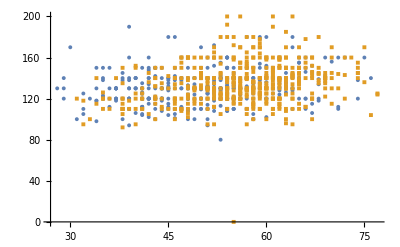
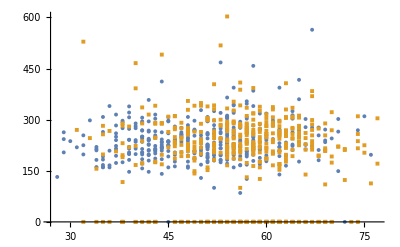
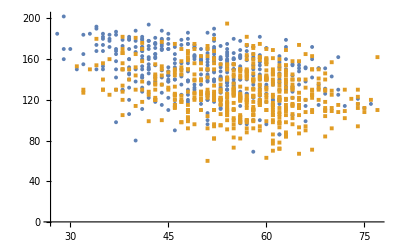
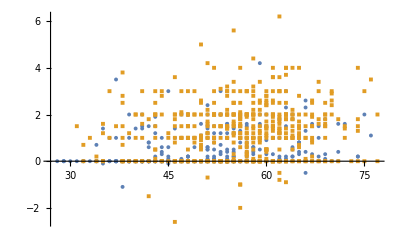
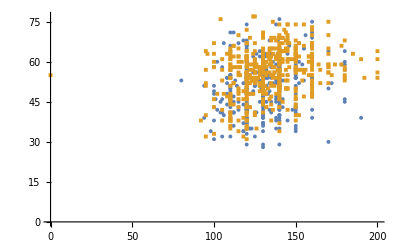
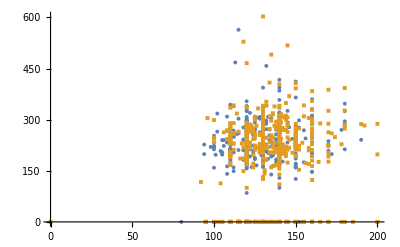
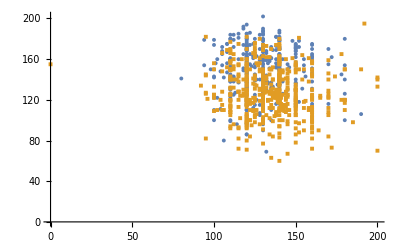
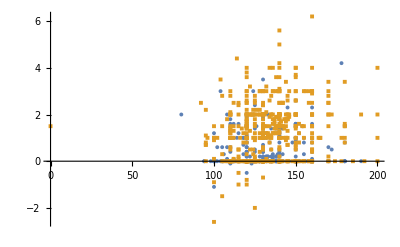
Age | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | RestingBP | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | Cholesterol | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | MaxHR | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | Oldpeak

```mathematica
Column[{Grid[Table[If[f1==f2,f2,ListPlot[{Values[Query[All, {f1,f2}][continousheartgrouped[[1]]]],Values[Query[All, {f1,f2}][continousheartgrouped[[2]]]]}, PlotMarkers->{Automatic, 4}]],{f1, columnheadings},{f2, columnheadings} ]],

PointLegend[ColorData[97,"ColorList"][[1;;2]],{0,1},LegendLayout->"Row",LegendMarkers->{Automatic, Small},LegendFunction->"Frame",LegendLabel->"Heart Disease"]},Alignment->Center]
```

```mathematica
columnheadings
```

{Age,RestingBP,Cholesterol,MaxHR,Oldpeak}

```mathematica
corr = Table[If[ v1==v2,1,N[Correlation[Transpose[Values[Query[All, {v1,v2}][heart2]]][[1]],Transpose[Values[Query[All, {v1,v2}][heart2]]][[2]]],3]], {v1,columnheadings},{v2,columnheadings}];
```

```mathematica
xlabel=Transpose[{Range[1,5],columnheadings}];
ylabel=Transpose[{Range[1,5],columnheadings}];
```

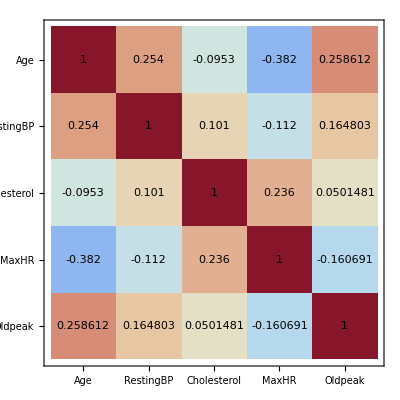

```mathematica
MatrixPlot[corr,
ColorFunction->"ThermometerColors",
Epilog->{Black,MapIndexed[Text[#1,Reverse[#2-1/2]]&,Reverse[corr],{2}]},
FrameTicks->{xlabel,ylabel}]
```

### Conclusions from multi variate analysis

There is a lack of distinct clusters in the scatter plots. There are some zones in the two dimensional space that are occupied more by subjects with heart disease, especially when considering Oldpeak and other variables, however the separation is still somewhat indistinct.

It is likely that the categorical variables will be more important in classification models.

The correlation matrix shows that non of the continuous Variables are strongly correlated

### Conclusion from exploratory data analysis

There are no Null values or duplicates in the dataset.

There is only one outlier to be removed.

A machine learning classifier model will be ideal for diagnosing heart disease.

None of the continuous variables are normally distributed, therefore a machine learning model that does not assume normality should be utilised. Tree based algorithms would be ideal.

However we will test the use of non- tree based algorithms as well, based on the classifier measurements the ideal model will be chosen.

All the categorical features have string values, these will be changed to numeric values using label encoding for tree-based models, and one hot encoding or dummy variables will be used for non-tree based models.

#### Categorical varaibles that need to be Label encoded.

```mathematica
Query[All, 3][heart]// DeleteDuplicates (* TA:Typical Angina, ATA:Atypical Angina, NAP:Non-Anginal Pain,ASY:Asymptomatic *)(*ATA = 1, NAP =2, ASY =3, TA = 4}*)
```

{ChestPainType,ATA,NAP,ASY,TA}

```mathematica
Query[All, 2][heart]// DeleteDuplicates(*M =0,F=1*)
```

{Sex,M,F}

```mathematica
Query[All, 7][heart]// DeleteDuplicates (*"Normal"=1,"ST"=2,"LVH"=3*)
```

{RestingECG,Normal,ST,LVH}

```mathematica
Query[2;;, 9][heart]// DeleteDuplicates (*N,Y : 0 = N and Y = 1 *)
```

{N,Y}

```mathematica
Query[2;;, -2][heart]// DeleteDuplicates (*{"Up"=1,"Flat"=2,"Down"=3} *)
```

{Up,Flat,Down}

First task is to remove the identified outlier and Label Encode the categorical variables, the function below will automate this process.

```mathematica
cleanfunctions[data_List,sex_List,chestpain_List,ecg_List,angina_List,st_List] := Module[{clean1,clean2,clean3,clean4,clean5,clean6},
fs[s_] := If[s== "M", 0,1];(*changing M to 0 and F to 1 in sex variable*)
clean1=MapAt[fs,data,sex];(*Map the fs function onto the dataset at column sex and store in variable clean1*)
f[cp_]:=Which[cp == "ATA", 1, cp == "NAP",2 ,cp== "ASY",3, cp== "TA",4];(*Where the value is ATA  change to 1 , NAP to 2, ASY to 3 and TA to 4 in the ChestPainType column*)
clean2=MapAt[f,clean1,chestpain];(*Map the f function to dataset clean1 at the ChestPainType column and save to clean2*)
fecg[e_]:=Which[e == "Normal", 1, e == "ST",2 ,e== "LVH",3];(*Where the value is Normal  change to 1 , St to 2, LVH to 3 in the ecg column*)
clean3=MapAt[fecg,clean2,ecg];(*Map the fecg function to the dataset clean2 at the RestingECG column*)
fea[ea_] := If[ea== "N", 0,1];(*Where the value in column is N change to 0 if not change to 1*)
clean4=MapAt[fea,clean3,angina];
fst[t_]:=Which[t == "Up", 1, t == "Flat",2 ,t== "Down",3];clean5=MapAt[fst,clean4,st];clean6 =AssociationThread[clean5[[1]]-> #]& /@ clean5[[2;;]];(*Thread the first row columns onto all respective columns*)
Return[clean6]](*This function will convert all  columns containing strings into numerical values (indices), taking the dataframe as the first argument, and subsequent arguments being the rows and columns of the variable that needs change, going from left to right , it also threads an association using the first row as a set of keys for the whole dataset*)
```

```mathematica
heartdata=cleanfunctions[heart,{2;;, 2},{2;;, 3},{2;;, 7} ,{2;;, 9} ,{2;;, -2}]
```

{<|Age→40,Sex→0,ChestPainType→1,RestingBP→140,Cholesterol→289,FastingBS→0,RestingECG→1,MaxHR→172,ExerciseAngina→0,Oldpeak→0,ST_Slope→1,HeartDisease→0|>,<|Age→49,Sex→1,ChestPainType→2,RestingBP→160,Cholesterol→180,FastingBS→0,RestingECG→1,MaxHR→156,ExerciseAngina→0,Oldpeak→1,ST_Slope→2,HeartDisease→1|>,915,<|Age→38,Sex→0,ChestPainType→2,RestingBP→138,Cholesterol→175,FastingBS→0,RestingECG→1,MaxHR→173,ExerciseAngina→0,Oldpeak→0,ST_Slope→1,HeartDisease→0|>}
 |  |  |  |

```mathematica
Position[heartdata, <|___, "RestingBP"-> 0,___|>]// Flatten (*The row containing RestingBP = 0*)
```

{450}

```mathematica
hdf =Drop[heartdata,  {450}](*Drop the row iwht outlier, Dataset ready for modeling*)
```

{<|Age→40,Sex→0,ChestPainType→1,RestingBP→140,Cholesterol→289,FastingBS→0,RestingECG→1,MaxHR→172,ExerciseAngina→0,Oldpeak→0,ST_Slope→1,HeartDisease→0|>,<|Age→49,Sex→1,ChestPainType→2,RestingBP→160,Cholesterol→180,FastingBS→0,RestingECG→1,MaxHR→156,ExerciseAngina→0,Oldpeak→1,ST_Slope→2,HeartDisease→1|>,914,<|Age→38,Sex→0,ChestPainType→2,RestingBP→138,Cholesterol→175,FastingBS→0,RestingECG→1,MaxHR→173,ExerciseAngina→0,Oldpeak→0,ST_Slope→1,HeartDisease→0|>}
 |  |  |  |

```mathematica
variablelist =Keys[hdf]// DeleteDuplicates// Flatten
```

{Age,Sex,ChestPainType,RestingBP,Cholesterol,FastingBS,RestingECG,MaxHR,ExerciseAngina,Oldpeak,ST_Slope,HeartDisease}

The function below will automate the process of obtaining datasets and list that contain the variable of interest for performing statistical tests and graphical representation

```mathematica
variablesplit[var_, dataname_,negativename_,positivename_] := (*Function will take the variable name we need to isolate at var_, the name of the dataset with the isolated data in dataname, the name of the list containing values of from the specified column for subjects that do not have heartdisease at negativename_, and the values for all subjects that have a positive diagnosis in positivename_*)Module[{all,negvalue,posvalue}, all = GroupBy[Query[ All,{var,"HeartDisease"}] [heartdata], #HeartDisease&];(*obtain all rows in dataset, and only columns that have the key HEartDisease and the desired column according to input at var, and then group them according to Value in HeartDisease, this dataset is called all*)dataname = all;(*The dataset all that was made before, is assigned to variable dataname ie. the second function argument*)negvalue= Values[all][[1]][[All,1]]// Sort;(*take values from the all dataset, this dataset is an association of a association, since its grouped by heartdisease therefore when we take Values of this nested association it gives us a nested list with two lists or teo rows, take this nested list and get the first row, that corrosponds to the group that were negatively diagnosed, then take all the rows and the 1st column from this matrix, which gives us a list containing all the variable values that we need for subjects with a negative diagnosis, asign this list to a variable that is given in the negativename argument of the function *)negativename = negvalue; posvalue= Values[all][[2]][[All,1]]// Sort;(*Same process used in the previous function for obtaining values, now for all the patients with a positive diagnosis*)positivename=posvalue;Return[dataname];
Return[negativename];Return[positivename]]
```

### Model Fitting

The splitfunction[], will automatically split the dataset into training and testing data, and group them into HeartDisease 0 or 1, function input is the dataset as the first variable , the desired names of the training and testing datasets and second and third variables respectively.
The data will be split 80/20 into training and testing sets respectively.

```mathematica
splitfunction[heartdata_,trainname_,testname_ ]:= Module[ {train,test },
RandomSeed[1234];train = RandomSample[heartdata, 734];test = Complement[heartdata,train];
 trainname = Drop[GroupBy[train, #"HeartDisease"&],None,None,{-1}] ; testname= Drop[GroupBy[test, #"HeartDisease"&],None,None,{-1}] ]
```

First classifier models will input the hdf data as is, this in order to find feature importance and algorithms that work, These initial models will use a mixture of tree based and non tree based models.

```mathematica
ClearAll[train1,test1]
```

```mathematica
splitfunction[hdf,train1,test1];
```

```mathematica
testlist= {"RandomForest","LogisticRegression","NaiveBayes","NeuralNetwork"}(*These are the models that will be tested on the data*)
```

{RandomForest,LogisticRegression,NaiveBayes,NeuralNetwork}

```mathematica
ClearAll[c1,cm1]
```

```mathematica
modelmaker[traindata_,testdata_,modelsname_,measurement_] := Module[{models,measurements}, models = Table[Classify[traindata, Method-> #1] & /@  testlist];modelsname=models;measurements =ClassifierMeasurements[#,testdata]&/@ modelsname; measurement = measurements;Return[modelsname];Return[measurement]]
```

```mathematica
modelmaker[train1,test1,c1,cm1]
```

{ClassifierFunction[…],ClassifierFunction[…],ClassifierFunction[…],ClassifierFunction[…]}

```mathematica
metrics ={"Accuracy","AreaUnderROCCurve","FalseNegativeRate","ConfusionMatrixPlot"}(*Classifier measurments that will be used to asses effectiveness of models*)
```

{Accuracy,AreaUnderROCCurve,FalseNegativeRate,ConfusionMatrixPlot}

```mathematica
measuremaker[cm_]:= TableForm[Transpose[Table[cm[[x]][y], {x, Range[Length[cm]]},{y, metrics}]], TableHeadings->{metrics,testlist}](*Will make a convienent table for comparison of classifier measurement, taking the variable where classifier measurments are stored as an argument*)
```

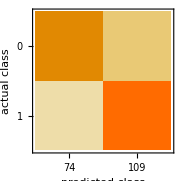
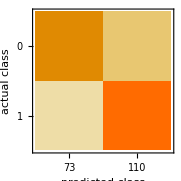
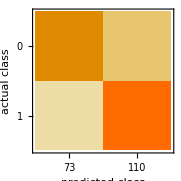
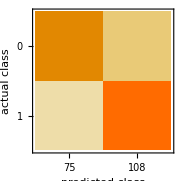
| RandomForest | LogisticRegression | NaiveBayes | NeuralNetwork
Accuracy | 0.857923 | 0.84153 | 0.830601 | 0.863388
AreaUnderROCCurve | <|0→0.905097,1→0.920267|> | <|0→0.919903,1→0.919903|> | <|0→0.89915,1→0.89915|> | <|0→0.917476,1→0.917476|>
FalseNegativeRate | <|0→0.2,1→0.0970874|> | <|0→0.225,1→0.106796|> | <|0→0.2375,1→0.116505|> | <|0→0.1875,1→0.0970874|>
ConfusionMatrixPlot | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
measuremaker[cm1]
```

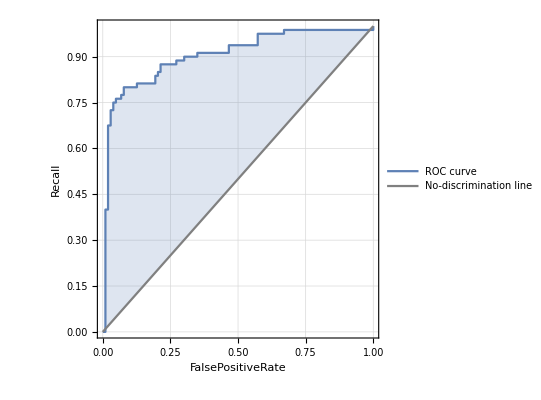
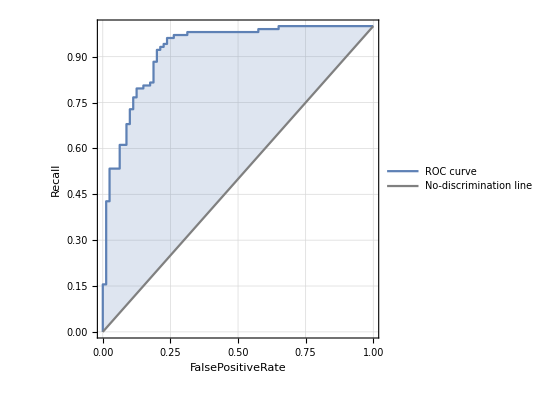
<|0→-Graphics-,1→-Graphics-|>

```mathematica
cm1[[1]]["ROCCurve"]
```

```mathematica
cm1 (*accuracy and number confusion matrix for each model, Random Forest seems to be the most accurate in addition to having the least number of false negatives, and highest number of true positives, It is most important to increase true positives and decrease false negatives, true negatives and false postives are are not a priority, ie decrease alpha 2 (Type II) errors  *)
```

```mathematica
cm1[[1]]["SHAPPlots"](*SHAP plots for the Random Forest model*)
```

<|0→-Graphics-,1→-Graphics-|>

```mathematica
cm1[[-1]]["SHAPPlots"](*SHAP plots for the nueral network model*)
```

<|0→-Graphics-,1→-Graphics-|>

Shapely value plot indicated that Age and Sex may not have a significant effect on the target variable. I will test wether removing this feature will improve model.

#### Removing Age feature from data

The Age variable will  be removed from the classifier function, Biologically age is a relevant variable . The risk of heart disease does increase with age , however for this data set the median age is between 60-50, and the number of subjects are not evenly spread around all age classes from 30 to 70.

```mathematica
hdf2 = hdf;
```

```mathematica
hdf2 =KeyDrop[hdf2, "Age"];
```

```mathematica
ClearAll[train2,test2,c2,cm2]
```

```mathematica
splitfunction[hdf2, train2,test2];
```

```mathematica
modelmaker[train2,test2,c2,cm2]
```

{ClassifierFunction[…],ClassifierFunction[…],ClassifierFunction[…],ClassifierFunction[…]}

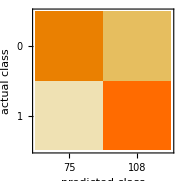
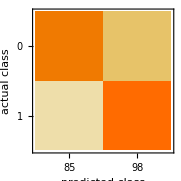
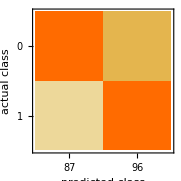
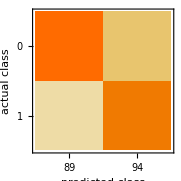
| RandomForest | LogisticRegression | NaiveBayes | NeuralNetwork
Accuracy | 0.84153 | 0.852459 | 0.852459 | 0.852459
AreaUnderROCCurve | <|0→0.929358,1→0.94205|> | <|0→0.935824,1→0.935824|> | <|0→0.937021,1→0.937021|> | <|0→0.929957,1→0.929957|>
FalseNegativeRate | <|0→0.260417,1→0.045977|> | <|0→0.197917,1→0.091954|> | <|0→0.1875,1→0.103448|> | <|0→0.177083,1→0.114943|>
ConfusionMatrixPlot | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
measuremaker[cm2]
```

Removing Age from the data  decreased false negative rate to 8%  when using the RandomForest model. Logistic Regression Model also improved.However, all other models decrease in effectiveness.

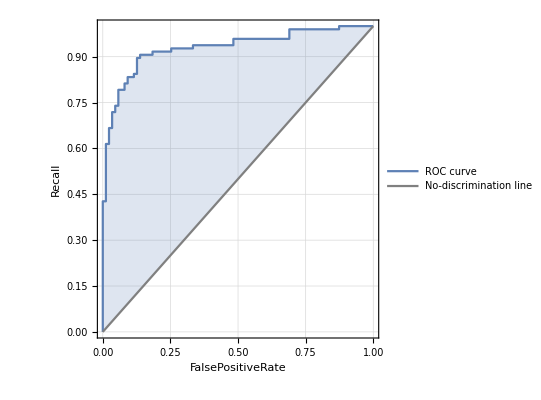
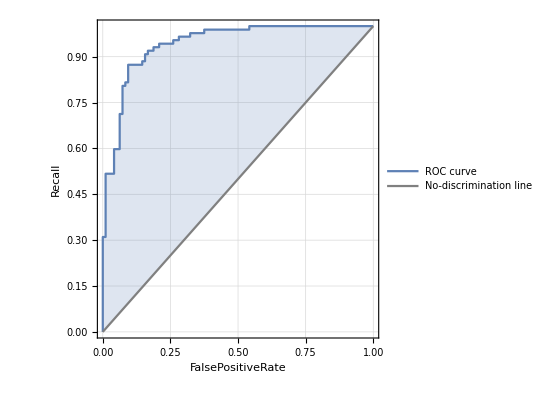
Cm1 | <|0→-Graphics-,1→-Graphics-|>
cm2 | <|0→-Graphics-,1→-Graphics-|>

```mathematica
TableForm[{cm1[[1]]["ROCCurve"],cm2[[1]]["ROCCurve"]}, TableHeadings->{{"Cm1","cm2"}}]
```

ROC curves also dispaly a slight improvement in prediction for diagnostic class 1.

#### Removing feature Sex from data

```mathematica
hdf3 = hdf;(*Duplicate the heart dataset in order to drop keys*)
```

```mathematica
hdf3 =KeyDrop[hdf3, "Sex"]
```

{<|Age→40,ChestPainType→1,RestingBP→140,Cholesterol→289,FastingBS→0,RestingECG→1,MaxHR→172,ExerciseAngina→0,Oldpeak→0,ST_Slope→1,HeartDisease→0|>,<|Age→49,ChestPainType→2,RestingBP→160,Cholesterol→180,FastingBS→0,RestingECG→1,MaxHR→156,ExerciseAngina→0,Oldpeak→1,ST_Slope→2,HeartDisease→1|>,<|Age→37,ChestPainType→1,RestingBP→130,Cholesterol→283,FastingBS→0,RestingECG→2,MaxHR→98,ExerciseAngina→0,Oldpeak→0,ST_Slope→1,HeartDisease→0|>,912,<|Age→57,ChestPainType→1,RestingBP→130,Cholesterol→236,FastingBS→0,RestingECG→3,MaxHR→174,ExerciseAngina→0,Oldpeak→0,ST_Slope→2,HeartDisease→1|>,<|Age→38,ChestPainType→2,RestingBP→138,Cholesterol→175,FastingBS→0,RestingECG→1,MaxHR→173,ExerciseAngina→0,Oldpeak→0,ST_Slope→1,HeartDisease→0|>}
 |  |  |  |

```mathematica
ClearAll[train3,test3,m3,cm3]
```

```mathematica
splitfunction[heart3, train3,test3];
```

```mathematica
modelmaker[train3,test3,m3,cm3]
```

{ClassifierFunction[…],ClassifierFunction[…],ClassifierFunction[…],ClassifierFunction[…]}

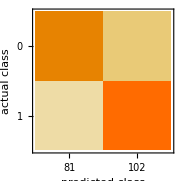
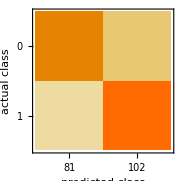
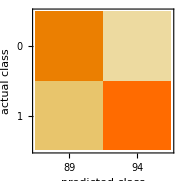
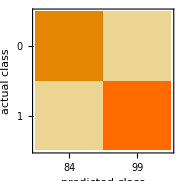
| RandomForest | LogisticRegression | NaiveBayes | NeuralNetwork
Accuracy | 0.863388 | 0.84153 | 0.830601 | 0.846995
AreaUnderROCCurve | <|0→0.934223,1→0.940236|> | <|0→0.912097,1→0.912097|> | <|0→0.919913,1→0.919913|> | <|0→0.916546,1→0.916546|>
FalseNegativeRate | <|0→0.166667,1→0.111111|> | <|0→0.190476,1→0.131313|> | <|0→0.154762,1→0.181818|> | <|0→0.166667,1→0.141414|>
ConfusionMatrixPlot | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
measuremaker[cm3]
```

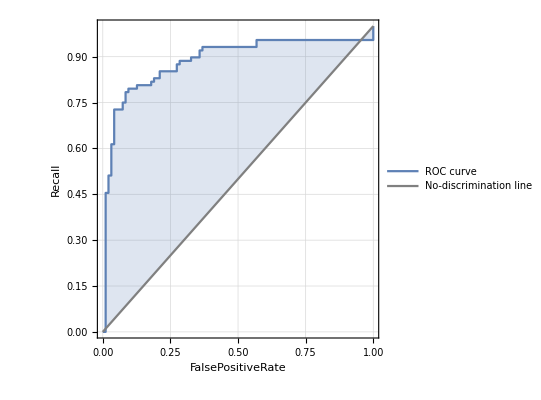
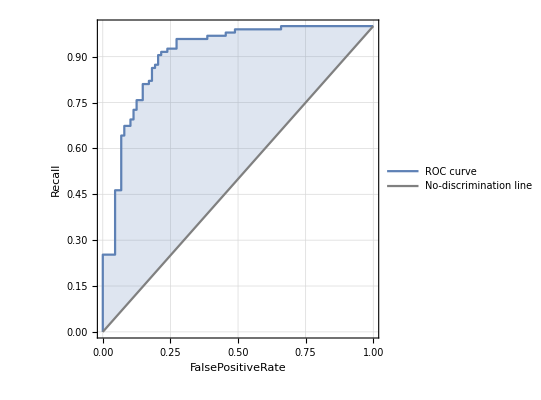
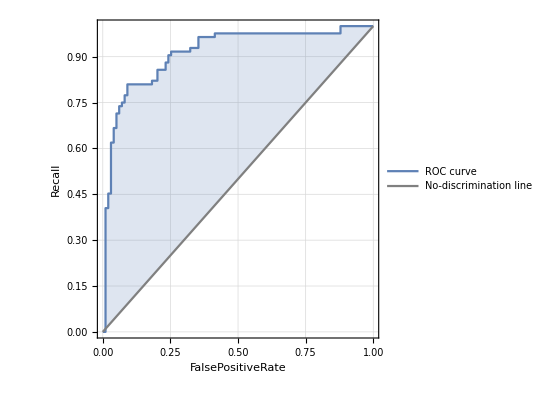
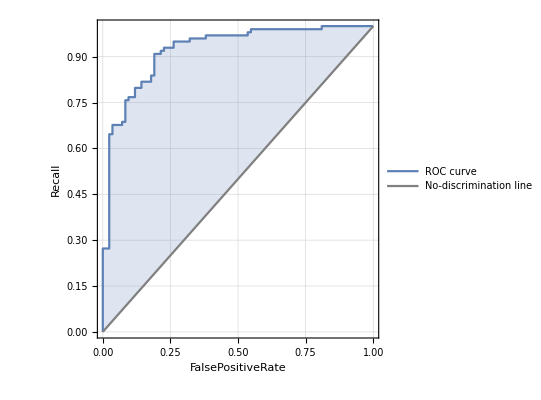
Cm1 | <|0→-Graphics-,1→-Graphics-|>
cm2 | <|0→-Graphics-,1→-Graphics-|>
cm3 | <|0→-Graphics-,1→-Graphics-|>

```mathematica
TableForm[{cm1[[1]]["ROCCurve"],cm2[[1]]["ROCCurve"], cm3[[1]]["ROCCurve"]}, TableHeadings->{{"Cm1","cm2","cm3"}}]
```

### Removing features Age & Sex from data

Attempt to drop both Age and Sex from the model to see if there is any effect on accuracy of the model.

```mathematica
hdf4 = hdf; (*Duplicate the heart dataset in order to drop keys*)
```

```mathematica
hdf4 =KeyDrop[heart4, {"Age","Sex"}]
```

{<|ChestPainType→1,RestingBP→140,Cholesterol→289,FastingBS→0,RestingECG→1,MaxHR→172,ExerciseAngina→0,Oldpeak→0,ST_Slope→1,HeartDisease→0|>,<|ChestPainType→2,RestingBP→160,Cholesterol→180,FastingBS→0,RestingECG→1,MaxHR→156,ExerciseAngina→0,Oldpeak→1,ST_Slope→2,HeartDisease→1|>,<|ChestPainType→1,RestingBP→130,Cholesterol→283,FastingBS→0,RestingECG→2,MaxHR→98,ExerciseAngina→0,Oldpeak→0,ST_Slope→1,HeartDisease→0|>,912,<|ChestPainType→1,RestingBP→130,Cholesterol→236,FastingBS→0,RestingECG→3,MaxHR→174,ExerciseAngina→0,Oldpeak→0,ST_Slope→2,HeartDisease→1|>,<|ChestPainType→2,RestingBP→138,Cholesterol→175,FastingBS→0,RestingECG→1,MaxHR→173,ExerciseAngina→0,Oldpeak→0,ST_Slope→1,HeartDisease→0|>}
 |  |  |  |

```mathematica
ClearAll[ train4,test4,m4,cm4]
```

```mathematica
splitfunction[heart4, train4,test4];
```

```mathematica
modelmaker[train4,test4,m4,cm4]
```

{ClassifierFunction[…],ClassifierFunction[…],ClassifierFunction[…],ClassifierFunction[…]}

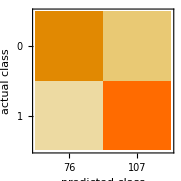
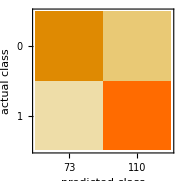
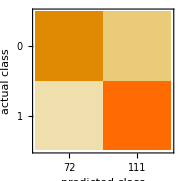
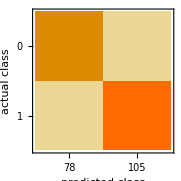
| RandomForest | LogisticRegression | NaiveBayes | NeuralNetwork
Accuracy | 0.836066 | 0.852459 | 0.879781 | 0.857923
AreaUnderROCCurve | <|0→0.906227,1→0.915629|> | <|0→0.926129,1→0.926129|> | <|0→0.925031,1→0.925031|> | <|0→0.919048,1→0.919048|>
FalseNegativeRate | <|0→0.205128,1→0.133333|> | <|0→0.205128,1→0.104762|> | <|0→0.179487,1→0.0761905|> | <|0→0.166667,1→0.12381|>
ConfusionMatrixPlot | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
measuremaker[cm4]
```

### Turning Age into a continuous variable

Grouping age into different categories

```mathematica
agegrouper[aged_]:= Which[aged >=28 && aged <=39, 1,
 aged>= 40 && aged<= 49, 2,
 aged>= 50 && aged <= 59,3, 
aged>= 60 && aged<= 69,4,
aged>=70 && aged <=77,5]
```

```mathematica
h3=MapAt[agegrouper,heart,{2;;,1}]
```

{{Age,Sex,ChestPainType,RestingBP,Cholesterol,FastingBS,RestingECG,MaxHR,ExerciseAngina,Oldpeak,ST_Slope,HeartDisease},{2,M,ATA,140,289,0,Normal,172,N,0,Up,0},{2,F,NAP,160,180,0,Normal,156,N,1,Flat,1},{1,M,ATA,130,283,0,ST,98,N,0,Up,0},{2,F,ASY,138,214,0,Normal,108,Y,1.5,Flat,1},910,{4,M,ASY,144,193,1,Normal,141,N,3.4,Flat,1},{3,M,ASY,130,131,0,Normal,115,Y,1.2,Flat,1},{3,F,ATA,130,236,0,LVH,174,N,0,Flat,1},{1,M,NAP,138,175,0,Normal,173,N,0,Up,0}}
 |  |  |  |

```mathematica
heart5 =cleanfunctions[h3,{2;;, 2},{2;;, 3}, {2;;, 7},{2;;, 9},{2;;, 11} ]
```

{<|Age→2,Sex→0,ChestPainType→1,RestingBP→140,Cholesterol→289,FastingBS→0,RestingECG→1,MaxHR→172,ExerciseAngina→0,Oldpeak→0,ST_Slope→1,HeartDisease→0|>,<|Age→2,Sex→1,ChestPainType→2,RestingBP→160,Cholesterol→180,FastingBS→0,RestingECG→1,MaxHR→156,ExerciseAngina→0,Oldpeak→1,ST_Slope→2,HeartDisease→1|>,915,<|Age→1,Sex→0,ChestPainType→2,RestingBP→138,Cholesterol→175,FastingBS→0,RestingECG→1,MaxHR→173,ExerciseAngina→0,Oldpeak→0,ST_Slope→1,HeartDisease→0|>}
 |  |  |  |

```mathematica
ClearAll[h5train,h5test,h5model,h5metrics]
```

```mathematica
splitfunction[heart5, h5train,h5test];
```

```mathematica
modelmaker[h5train,h5test,h5model,h5metrics]
```

{ClassifierFunction[…],ClassifierFunction[…],ClassifierFunction[…],ClassifierFunction[…]}

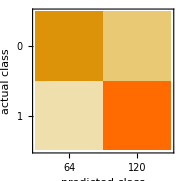
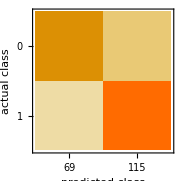
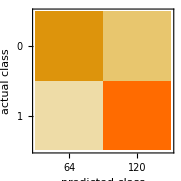
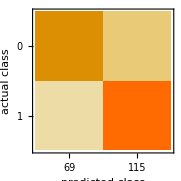
| RandomForest | LogisticRegression | NaiveBayes | NeuralNetwork
Accuracy | 0.853261 | 0.836957 | 0.820652 | 0.847826
AreaUnderROCCurve | <|0→0.904727,1→0.919042|> | <|0→0.896582,1→0.896582|> | <|0→0.883006,1→0.883006|> | <|0→0.90448,1→0.90448|>
FalseNegativeRate | <|0→0.246575,1→0.0810811|> | <|0→0.232877,1→0.117117|> | <|0→0.287671,1→0.108108|> | <|0→0.219178,1→0.108108|>
ConfusionMatrixPlot | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
measuremaker[h5metrics]
```

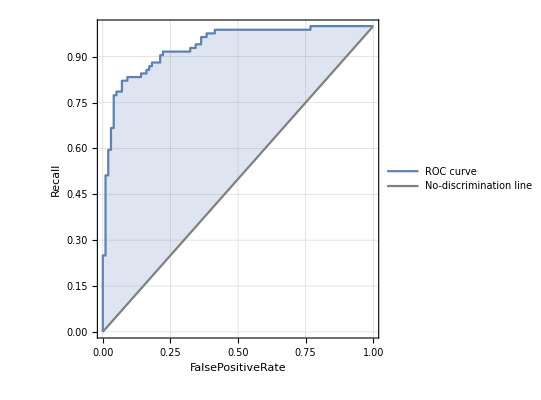
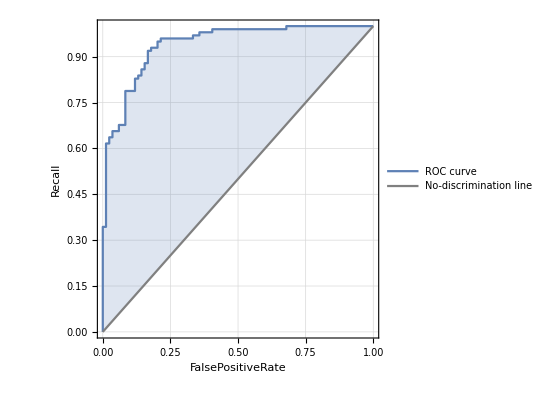
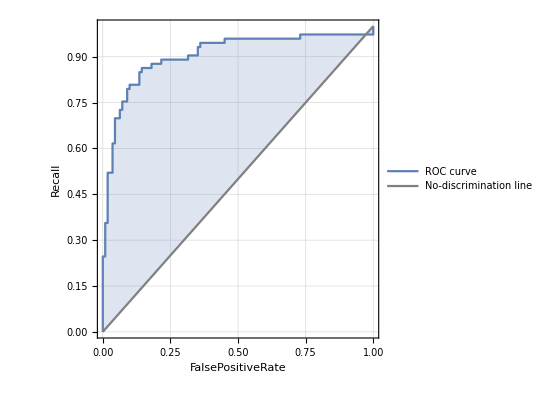
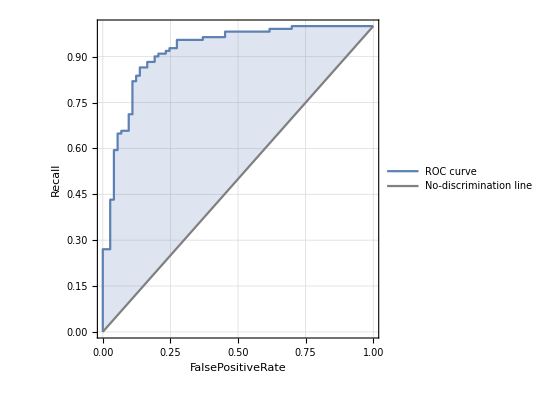
Cm1 | <|0→-Graphics-,1→-Graphics-|>
cm2 | <|0→-Graphics-,1→-Graphics-|>
cm3 | <|0→-Graphics-,1→-Graphics-|>
h5model | <|0→-Graphics-,1→-Graphics-|>

```mathematica
TableForm[{cm1[[1]]["ROCCurve"],cm2[[1]]["ROCCurve"], cm3[[1]]["ROCCurve"],h5metrics[[1]]["ROCCurve"]}, TableHeadings->{{"Cm1","cm2","cm3","h5model"}}]
```

```mathematica
measuremaker[cm_]:= TableForm[Transpose[Table[cm[[x]][y], {x, Range[Length[cm]]},{y, metrics}]], TableHeadings->{metrics,testlist}](*Will make a convienent table for comparison of classifier measurements*)
```

```mathematica
modellist ={cm1,cm2,cm3,cm4,h5metrics};
```

```mathematica
TableForm[Transpose[Table[cm[[1]][y],{cm,modellist } ,{y, metrics}]], TableHeadings->{metrics,{"cm1","cm2","cm3","cm4","h5metrics"}}]
```

| cm1 | cm2 | cm3 | cm4 | h5metrics
Accuracy | 0.857923 | 0.84153 | 0.863388 | 0.836066 | 0.853261
AreaUnderROCCurve | <|0→0.905097,1→0.920267|> | <|0→0.929358,1→0.94205|> | <|0→0.934223,1→0.940236|> | <|0→0.906227,1→0.915629|> | <|0→0.904727,1→0.919042|>
FalseNegativeRate | <|0→0.2,1→0.0970874|> | <|0→0.260417,1→0.045977|> | <|0→0.166667,1→0.111111|> | <|0→0.205128,1→0.133333|> | <|0→0.246575,1→0.0810811|>
ConfusionMatrixPlot | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Out of all the trained models h5model had the best performance, with a AOC of 0.94 and a FNR of 0.08.

### Data Visualisations for Report

```mathematica
BarChart[{Callout[410,"44.66%" ],Callout[508, "55.34%"]},{ChartStyle-> {Green, Red}, ChartLabels->{"Healthy", "Heart Disease"}, AxesLabel-> "Counts", LabelStyle->Directive[Bold, Thick]}]
```

-Graphics-

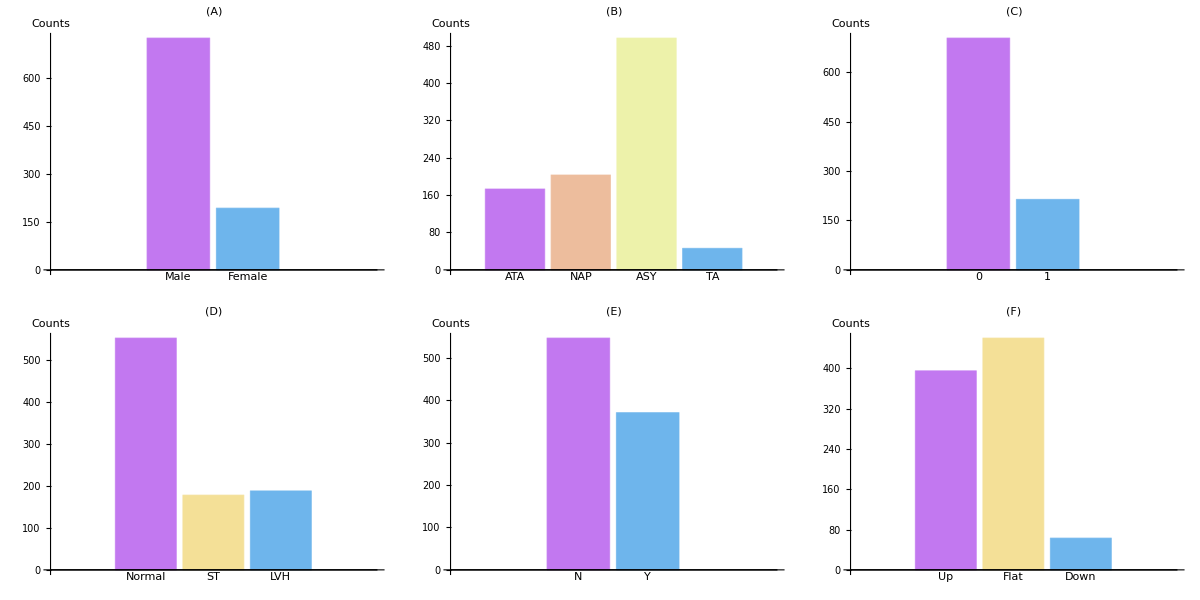

```mathematica
Grid[{{BarChart[gengdata,{ChartStyle-> "Pastel", ChartLabels->{"Male","Female"}, AxesLabel-> "Counts", PlotLabel-> "(A)", LabelStyle->Directive[Bold, Thick]}],BarChart[paindata,{ChartStyle-> "Pastel", ChartLabels->Automatic, AxesLabel-> "Counts", PlotLabel->"(B)", LabelStyle->Directive[Bold, Thick]}],
BarChart[bstally,{ChartStyle-> "Pastel", ChartLabels->Automatic, AxesLabel-> "Counts", PlotLabel->"(C)", LabelStyle->Directive[Bold, Thick]}]},
{BarChart[ecgtally,{ChartStyle-> "Pastel", ChartLabels->Automatic, AxesLabel-> "Counts", PlotLabel->"(D)", LabelStyle->Directive[Bold, Thick]}],
BarChart[angtally,{ChartStyle-> "Pastel", ChartLabels->Automatic, AxesLabel-> "Counts", PlotLabel->"(E)", LabelStyle->Directive[Bold, Thick]}],
BarChart[sttally,{ChartStyle-> "Pastel", ChartLabels->Automatic, AxesLabel-> "Counts", PlotLabel->"(F)", LabelStyle->Directive[Bold, Thick]}]}}]
```

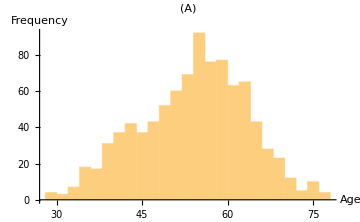
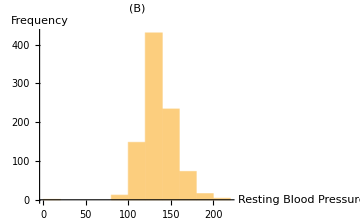
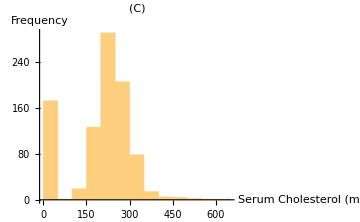
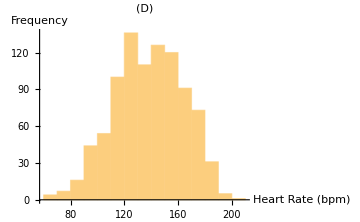
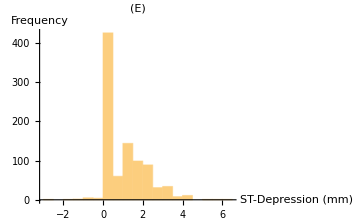
-Graphics- | 
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[{{Histogram[loneage, AxesLabel->{"Age", "Frequency"}, PlotLabel->"(A)", ImageSize->Medium]},
 {Histogram[lonebp, AxesLabel-> {"Resting Blood Pressure(mmHg)", "Frequency"},PlotLabel->"(B)" ,ImageSize->Medium],
Histogram[lonechol,AxesLabel->{"Serum Cholesterol (mg/dl)","Frequency"},PlotLabel->"(C)" , ImageSize->Medium]},
{Histogram[lonehr, AxesLabel-> {"Heart Rate (bpm)","Frequency"},PlotLabel->"(D)" , ImageSize->Medium],
Histogram[loneold, AxesLabel-> {"ST-Depression (mm)","Frequency"},PlotLabel->"(E)" , ImageSize->Medium]}}]
```

```mathematica
Column[{Row[{BoxWhiskerChart[{age0,age1}, {"Outliers",{"MedianMarker",1,Directive[Thick,Red]}} ,ChartStyle->ColorData[97,"ColorList"][[1;;2]], ImageSize->Medium],DistributionChart[{age0,age1},ChartStyle->ColorData[97,"ColorList"][[1;;2]], ImageSize->Medium]}],PointLegend[ColorData[97,"ColorList"][[1;;2]],{0,1},LegendLayout->"Row",LegendMarkers->{Automatic, Small},LegendFunction->"Frame",LegendLabel->"Heart Disease"]},Alignment->Center]
```

-Graphics--Graphics-

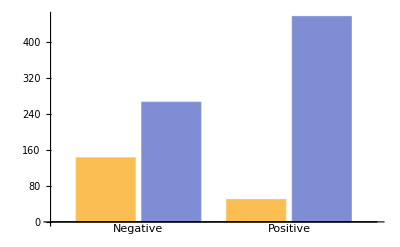

```mathematica
BarChart[<|s0ta,s1ta|>, ChartLabels->{{"Negative","Positive"},None}]
```

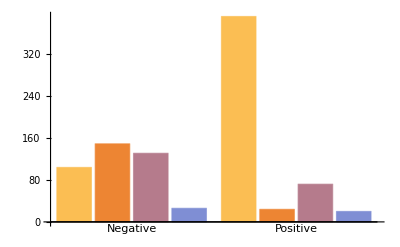

```mathematica
BarChart[<|cpt0ta,cpt1ta|>, ChartLabels->{{"Negative","Positive"},None}]
```

```mathematica
GraphicsGrid[{{"(A)", "(B)"},Table[cm1[[x]]["ConfusionMatrixPlot"], {x, Length[cm1]}][[;;2]],{"(C)", "(D)"},Table[cm1[[x]]["ConfusionMatrixPlot"], {x, Length[cm1]}][[3;;]]}]
```

(A) | (B)
-Graphics- | -Graphics-
(C) | (D)
-Graphics- | -Graphics-

```mathematica
measuremaker[cm_]:= TableForm[Transpose[Table[cm[[x]][y], {x, Range[Length[cm]]},{y, metrics}]], TableHeadings->{metrics,testlist}]
```

```mathematica
TableForm[Transpose[Table[cm1[[x]][y], {x, Length[cm1]}, {y, metrics[[;;-2]]}]], TableHeadings->{metrics,testlist}]
```

| RandomForest | LogisticRegression | NaiveBayes | NeuralNetwork
Accuracy | 0.857923 | 0.84153 | 0.830601 | 0.863388
AreaUnderROCCurve | <|0→0.905097,1→0.920267|> | <|0→0.919903,1→0.919903|> | <|0→0.89915,1→0.89915|> | <|0→0.917476,1→0.917476|>
FalseNegativeRate | <|0→0.2,1→0.0970874|> | <|0→0.225,1→0.106796|> | <|0→0.2375,1→0.116505|> | <|0→0.1875,1→0.0970874|>

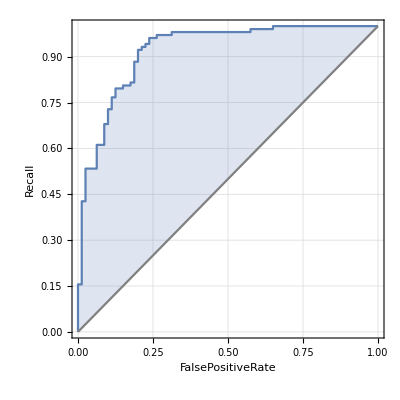
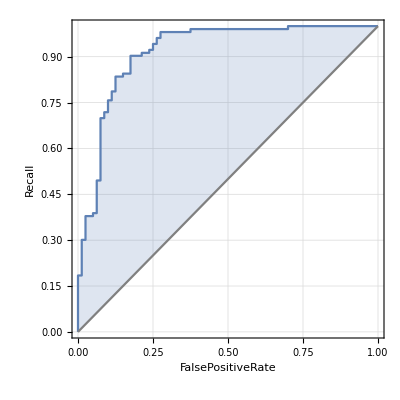
```mathematica
Grid[{{"(A)","(B)"},{-Graphics-,-Graphics-}}]
```

(A) | (B)
-Graphics- | -Graphics-

$Aborted

```mathematica
Grid[{{"(A)", "(B)"},Table[cm2[[x]]["ConfusionMatrixPlot"], {x, Length[cm2]}][[;;2]],{"(C)", "(D)"},Table[cm2[[x]]["ConfusionMatrixPlot"], {x, Length[cm2]}][[3;;]]}]
```

(A) | (B)
-Graphics- | -Graphics-
(C) | (D)
-Graphics- | -Graphics-

```mathematica
TableForm[Transpose[Table[cm2[[x]][y], {x, Length[cm1]}, {y, metrics[[;;-2]]}]], TableHeadings->{metrics,testlist}]
```

| RandomForest | LogisticRegression | NaiveBayes | NeuralNetwork
Accuracy | 0.84153 | 0.852459 | 0.852459 | 0.852459
AreaUnderROCCurve | <|0→0.929358,1→0.94205|> | <|0→0.935824,1→0.935824|> | <|0→0.937021,1→0.937021|> | <|0→0.929957,1→0.929957|>
FalseNegativeRate | <|0→0.260417,1→0.045977|> | <|0→0.197917,1→0.091954|> | <|0→0.1875,1→0.103448|> | <|0→0.177083,1→0.114943|>

```mathematica
cm2[[1]]["ROCCurve"]
```

<|0→-Graphics-,1→-Graphics-|>

```mathematica
TableForm[Transpose[Table[cm[[1]][y],{cm,modellist } ,{y, metrics}]], TableHeadings->{metrics,{"cm1","cm2","cm3","cm4","h5metrics"}}]
```

| cm1 | cm2 | cm3 | cm4 | h5metrics
Accuracy | 0.857923 | 0.84153 | 0.863388 | 0.836066 | 0.853261
AreaUnderROCCurve | <|0→0.905097,1→0.920267|> | <|0→0.929358,1→0.94205|> | <|0→0.934223,1→0.940236|> | <|0→0.906227,1→0.915629|> | <|0→0.904727,1→0.919042|>
FalseNegativeRate | <|0→0.2,1→0.0970874|> | <|0→0.260417,1→0.045977|> | <|0→0.166667,1→0.111111|> | <|0→0.205128,1→0.133333|> | <|0→0.246575,1→0.0810811|>
ConfusionMatrixPlot | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
BarChart[{Callout[{0.858,0.920,-0.097},"A"],Callout[{0.842,0.942,-0.046},"B"],Callout[ {0.836,0.916,-0.133},"C"],Callout[{0.853,0.919,-0.081},"D"]},ChartStyle-> {Green, Blue , Red}, AxesOrigin -> {0,0}, ChartLegends->{"Accuracy", "Area Under ROC Curve", "False Negative Rate"}]
```

-Graphics-